```mathematica
CreatePacletArchive[FileNameJoin[{NotebookDirectory[],"ggplot"}],FileNameJoin[{NotebookDirectory[],"Paclet"}]];
PacletInstall[%]
```

PacletInstall::samevers: A paclet named ggplot with the same version number (0.2) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

$Failed

```mathematica
PacletUninstall["ggplot"]
```

```mathematica
PacletUninstall[ggplot]
```

PacletUninstall[ggplot]

```mathematica
Quit[]
```

```mathematica
Get["ggplot`ggplot`"]
```

```mathematica
<<ggplot`
```

Set theme to ggplotThemePub

## Misc. Definitions

op - which allows for an easy way to turn a function into an operator and op2 - which is similar to op, however, the second argument is the one that is assumed to be “piped” in

```mathematica
SetAttributes[op, HoldAllComplete];
op[head_][expr___]          := head[expr];
op[head_[args___]][expr___] := head[expr, args];

SetAttributes[op2, HoldAllComplete];
op2[head_][expr___]       := head[expr];
op2[head_[expr_]][args_]  := head[expr, args];
```

tidyExpression: Convenient function for “tidying up” data meaning to get data into a list of associations for easy ability to work in Wolfram Language.

```mathematica
(*tidyExpression is a way to easily change some common data structures in WL into a tidy form (list of associations)*)(*{"value1","value2","value3"}->{<|Key1->value1,Key2->value2,Key3->value3|>}*)tidyExpression[expr_?(VectorQ[#,MatchQ[Except[_?ListQ|_?AssociationQ]]]&),lbls_]:=Flatten@List@AssociationThread[lbls,expr];
tidyExpression[lbls_][expr_?(VectorQ[#,MatchQ[Except[_?ListQ|_?AssociationQ]]]&)]:=tidyExpression[expr,lbls];

(*{{"value1-1","value2-1","value3-1"},{"value1-2","value2-2","value3-2"}}->{<|Key1->value1-1,Key2->value2-1,Key3->value3-1|>,<|Key1->value1-2,Key2->value2-2,Key3->value3-2|>}*)
tidyExpression[expr_?(MatrixQ[#,MatchQ[Except[_?AssociationQ]]]&),lbls_]:=Flatten@Map[AssociationThread[lbls,#]&,expr];
tidyExpression[lbls_][expr_?(MatrixQ[#,MatchQ[Except[_?AssociationQ]]]&)]:=tidyExpression[expr,lbls];

(*<|"value1-1"->"value1-2","value2-1"->"value2-2"|>->{<|Key1->value1-1,Key2->value1-2|>,<|Key1->value2-1,Key2->value2-2|>}*)
tidyExpression[assc_?AssociationQ,lbls_]/;MatchQ[assc,<|(_->Except[_?ListQ|_?AssociationQ])..|>]:=Flatten@ReplaceAll[Normal[assc],Rule[key_,value_]:>AssociationThread[lbls,{key,value}]];

(*<|"value1-1"->{"value1-2"},"value2-1"->{"value2-2"}|>->{<|Key1->value1-1,Key2->value1-2|>,<|Key1->value2-1,Key2->value2-2|>}*)
tidyExpression[assc_?AssociationQ,lbls_]/;MatchQ[assc,<|(_->_?(VectorQ[#,MatchQ[Except[_?ListQ|_?AssociationQ]]]&))..|>]:=Flatten@ReplaceAll[Normal[assc],Rule[key_,{values__}]:>AssociationThread[lbls,{key,values}]];

(*<|"value1-1"->{{"value1-2-1","value1-3-1"},{"value1-2-2","value1-3-2"}},"value2-1"->{{"value2-2-1","value2-3-1"},{"value2-2-2","value2-3-2"}}|>->{<|Key1->value1-1,Key2->value1-2-1,Key3->value1-3-1|>,<|Key1->value1-1,Key2->value1-2-2,Key3->value1-3-2|>,<|Key1->value2-1,Key2->value2-2-1,Key3->value2-3-1|>,<|Key1->value2-1,Key2->value2-2-2,Key3->value2-3-2|>}*)
tidyExpression[assc_?AssociationQ,lbls_]/;MatchQ[assc,<|(_->_?MatrixQ)..|>]:=Flatten@ReplaceAll[Normal[assc],Rule[key_,allValues:{{__}..}]:>Table[AssociationThread[lbls,{key,Sequence@@values}],{values,allValues}]];

(*<|"value1-1"-><|"Key2"->"value1-2"|>,"value2-1"-><|"Key2"->"value2-2"|>|>->{<|Key1->value1-1,Key2->value1-2|>,<|Key1->value2-1,Key2->value2-2|>}*)
tidyExpression[assc_?AssociationQ,lbl_]/;MatchQ[assc,<|(_->_?AssociationQ)..|>]:=Flatten@ReplaceAll[Normal[assc],Rule[key_,value_?AssociationQ]:>Prepend[value,lbl->key]];

(*<|"value1-1"->{<|"Key2"->"value1-2"|>,<|"Key2"->"value1-2"|>},"value2-1"->{<|"Key2"->"value2-2"|>,<|"Key2"->"value2-2"|>}|>->{<|Key1->value1-1,Key2->value1-2|>,<|Key1->value1-1,Key2->value1-2|>,<|Key1->value2-1,Key2->value2-2|>,<|Key1->value2-1,Key2->value2-2|>}*)
tidyExpression[assc_?AssociationQ,lbl_]/;MatchQ[assc,<|(_->{_?AssociationQ..})..|>]:=Flatten@ReplaceAll[Normal[assc],Rule[key_,value_?ListQ]:>Map[Prepend[#,lbl->key]&,value]];

(*Operator form*)
tidyExpression[lbls_][assc_?AssociationQ]:=tidyExpression[assc,lbls];
```

## Sample Datasets

```mathematica
mpg=;
mtcars=;
economics=;
dates=;
df=;
```

## Testing: geoms/scales/aesthetics

```mathematica
ticks2[ggplot`Private`yScaleType$80156,ggplot`Private`min$,ggplot`Private`max$,List[]]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

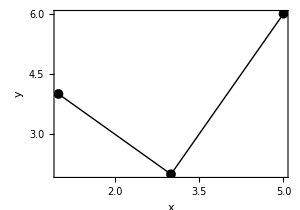

```mathematica
ggplot[df, "x"->"x", "y"->"y", geomPoint[], geomLine[]]
```

```mathematica
Charting
```

```mathematica
ticks2["Linear", 0, 5, {}]
```

ggplot`Private`formatTicks[Charting`ScaledTicks[Identity][0,5,{8,1}],{}]

```mathematica
FrameTicks
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

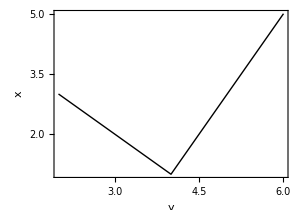

```mathematica
ggplot[df,"x"->"y","y"->"x",geomLine[]]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

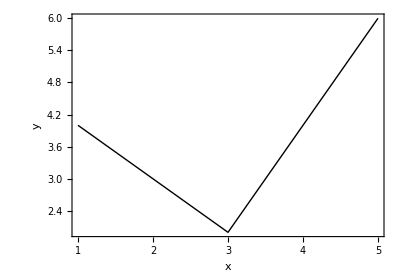

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

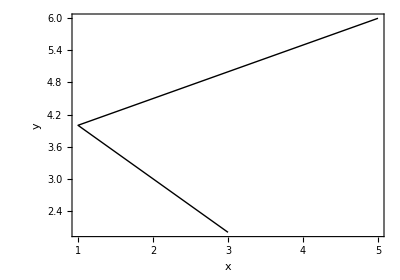

```mathematica
ggplot[df,"x"->"x","y"->"y",geomLine[]]
ggplot[df,"x"->"x","y"->"y",geomPath[]]
```

```mathematica
mpg//
	op[GroupBy[Function[#class]->Function[#hwy],Median]]//
	tidyExpression[{"class","hwy"}]//
	SortBy[Last]//
	ggplot["y"->"class","x"->"hwy",geomPoint[],numberOfMinorTicksPerMajorTick2->5]
```

GroupBy::list1: The argument (#class&)→(#hwy&) is not a valid list of Associations or rules or lists of rules.

ggplot[y→class,x→hwy,geomPoint[],numberOfMinorTicksPerMajorTick2→5][tidyExpression[{class,hwy}][op[GroupBy[(#class&)→(#hwy&),Median]][{<|manufacturer→audi,model→a4,displ→1.8,year→1999,cyl→4,trans→auto(l5),drv→f,cty→18,hwy→29,fl→p,class→compact|>,<|manufacturer→audi,model→a4,displ→1.8,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→p,class→compact|>,<|manufacturer→audi,model→a4,displ→2,year→2008,cyl→4,trans→manual(m6),drv→f,cty→20,hwy→31,fl→p,class→compact|>,<|manufacturer→audi,model→a4,displ→2,year→2008,cyl→4,trans→auto(av),drv→f,cty→21,hwy→30,fl→p,class→compact|>,<|manufacturer→audi,model→a4,displ→2.8,year→1999,cyl→6,trans→auto(l5),drv→f,cty→16,hwy→26,fl→p,class→compact|>,<|manufacturer→audi,model→a4,displ→2.8,year→1999,cyl→6,trans→manual(m5),drv→f,cty→18,hwy→26,fl→p,class→compact|>,<|manufacturer→audi,model→a4,displ→3.1,year→2008,cyl→6,trans→auto(av),drv→f,cty→18,hwy→27,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→1.8,year→1999,cyl→4,trans→manual(m5),drv→4,cty→18,hwy→26,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→1.8,year→1999,cyl→4,trans→auto(l5),drv→4,cty→16,hwy→25,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→2,year→2008,cyl→4,trans→manual(m6),drv→4,cty→20,hwy→28,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→2,year→2008,cyl→4,trans→auto(s6),drv→4,cty→19,hwy→27,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→2.8,year→1999,cyl→6,trans→auto(l5),drv→4,cty→15,hwy→25,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→2.8,year→1999,cyl→6,trans→manual(m5),drv→4,cty→17,hwy→25,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→3.1,year→2008,cyl→6,trans→auto(s6),drv→4,cty→17,hwy→25,fl→p,class→compact|>,<|manufacturer→audi,model→a4 quattro,displ→3.1,year→2008,cyl→6,trans→manual(m6),drv→4,cty→15,hwy→25,fl→p,class→compact|>,<|manufacturer→audi,model→a6 quattro,displ→2.8,year→1999,cyl→6,trans→auto(l5),drv→4,cty→15,hwy→24,fl→p,class→midsize|>,<|manufacturer→audi,model→a6 quattro,displ→3.1,year→2008,cyl→6,trans→auto(s6),drv→4,cty→17,hwy→25,fl→p,class→midsize|>,<|manufacturer→audi,model→a6 quattro,displ→4.2,year→2008,cyl→8,trans→auto(s6),drv→4,cty→16,hwy→23,fl→p,class→midsize|>,<|manufacturer→chevrolet,model→c1500 suburban 2wd,displ→5.3,year→2008,cyl→8,trans→auto(l4),drv→r,cty→14,hwy→20,fl→r,class→suv|>,<|manufacturer→chevrolet,model→c1500 suburban 2wd,displ→5.3,year→2008,cyl→8,trans→auto(l4),drv→r,cty→11,hwy→15,fl→e,class→suv|>,<|manufacturer→chevrolet,model→c1500 suburban 2wd,displ→5.3,year→2008,cyl→8,trans→auto(l4),drv→r,cty→14,hwy→20,fl→r,class→suv|>,<|manufacturer→chevrolet,model→c1500 suburban 2wd,displ→5.7,year→1999,cyl→8,trans→auto(l4),drv→r,cty→13,hwy→17,fl→r,class→suv|>,<|manufacturer→chevrolet,model→c1500 suburban 2wd,displ→6,year→2008,cyl→8,trans→auto(l4),drv→r,cty→12,hwy→17,fl→r,class→suv|>,<|manufacturer→chevrolet,model→corvette,displ→5.7,year→1999,cyl→8,trans→manual(m6),drv→r,cty→16,hwy→26,fl→p,class→2seater|>,<|manufacturer→chevrolet,model→corvette,displ→5.7,year→1999,cyl→8,trans→auto(l4),drv→r,cty→15,hwy→23,fl→p,class→2seater|>,<|manufacturer→chevrolet,model→corvette,displ→6.2,year→2008,cyl→8,trans→manual(m6),drv→r,cty→16,hwy→26,fl→p,class→2seater|>,<|manufacturer→chevrolet,model→corvette,displ→6.2,year→2008,cyl→8,trans→auto(s6),drv→r,cty→15,hwy→25,fl→p,class→2seater|>,<|manufacturer→chevrolet,model→corvette,displ→7,year→2008,cyl→8,trans→manual(m6),drv→r,cty→15,hwy→24,fl→p,class→2seater|>,<|manufacturer→chevrolet,model→k1500 tahoe 4wd,displ→5.3,year→2008,cyl→8,trans→auto(l4),drv→4,cty→14,hwy→19,fl→r,class→suv|>,<|manufacturer→chevrolet,model→k1500 tahoe 4wd,displ→5.3,year→2008,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→14,fl→e,class→suv|>,<|manufacturer→chevrolet,model→k1500 tahoe 4wd,displ→5.7,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→r,class→suv|>,<|manufacturer→chevrolet,model→k1500 tahoe 4wd,displ→6.5,year→1999,cyl→8,trans→auto(l4),drv→4,cty→14,hwy→17,fl→d,class→suv|>,<|manufacturer→chevrolet,model→malibu,displ→2.4,year→1999,cyl→4,trans→auto(l4),drv→f,cty→19,hwy→27,fl→r,class→midsize|>,<|manufacturer→chevrolet,model→malibu,displ→2.4,year→2008,cyl→4,trans→auto(l4),drv→f,cty→22,hwy→30,fl→r,class→midsize|>,<|manufacturer→chevrolet,model→malibu,displ→3.1,year→1999,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→chevrolet,model→malibu,displ→3.5,year→2008,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→29,fl→r,class→midsize|>,<|manufacturer→chevrolet,model→malibu,displ→3.6,year→2008,cyl→6,trans→auto(s6),drv→f,cty→17,hwy→26,fl→r,class→midsize|>,<|manufacturer→dodge,model→caravan 2wd,displ→2.4,year→1999,cyl→4,trans→auto(l3),drv→f,cty→18,hwy→24,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3,year→1999,cyl→6,trans→auto(l4),drv→f,cty→17,hwy→24,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.3,year→1999,cyl→6,trans→auto(l4),drv→f,cty→16,hwy→22,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.3,year→1999,cyl→6,trans→auto(l4),drv→f,cty→16,hwy→22,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.3,year→2008,cyl→6,trans→auto(l4),drv→f,cty→17,hwy→24,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.3,year→2008,cyl→6,trans→auto(l4),drv→f,cty→17,hwy→24,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.3,year→2008,cyl→6,trans→auto(l4),drv→f,cty→11,hwy→17,fl→e,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.8,year→1999,cyl→6,trans→auto(l4),drv→f,cty→15,hwy→22,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.8,year→1999,cyl→6,trans→auto(l4),drv→f,cty→15,hwy→21,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→3.8,year→2008,cyl→6,trans→auto(l6),drv→f,cty→16,hwy→23,fl→r,class→minivan|>,<|manufacturer→dodge,model→caravan 2wd,displ→4,year→2008,cyl→6,trans→auto(l6),drv→f,cty→16,hwy→23,fl→r,class→minivan|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→3.7,year→2008,cyl→6,trans→manual(m6),drv→4,cty→15,hwy→19,fl→r,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→3.7,year→2008,cyl→6,trans→auto(l4),drv→4,cty→14,hwy→18,fl→r,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→3.9,year→1999,cyl→6,trans→auto(l4),drv→4,cty→13,hwy→17,fl→r,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→3.9,year→1999,cyl→6,trans→manual(m5),drv→4,cty→14,hwy→17,fl→r,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→14,hwy→19,fl→r,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→14,hwy→19,fl→r,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→9,hwy→12,fl→e,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→5.2,year→1999,cyl→8,trans→manual(m5),drv→4,cty→11,hwy→17,fl→r,class→pickup|>,<|manufacturer→dodge,model→dakota pickup 4wd,displ→5.2,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→r,class→pickup|>,<|manufacturer→dodge,model→durango 4wd,displ→3.9,year→1999,cyl→6,trans→auto(l4),drv→4,cty→13,hwy→17,fl→r,class→suv|>,<|manufacturer→dodge,model→durango 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→13,hwy→17,fl→r,class→suv|>,<|manufacturer→dodge,model→durango 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→9,hwy→12,fl→e,class→suv|>,<|manufacturer→dodge,model→durango 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→13,hwy→17,fl→r,class→suv|>,<|manufacturer→dodge,model→durango 4wd,displ→5.2,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→16,fl→r,class→suv|>,<|manufacturer→dodge,model→durango 4wd,displ→5.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→13,hwy→18,fl→r,class→suv|>,<|manufacturer→dodge,model→durango 4wd,displ→5.9,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→r,class→suv|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→4.7,year→2008,cyl→8,trans→manual(m6),drv→4,cty→12,hwy→16,fl→r,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→9,hwy→12,fl→e,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→13,hwy→17,fl→r,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→13,hwy→17,fl→r,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→4.7,year→2008,cyl→8,trans→manual(m6),drv→4,cty→12,hwy→16,fl→r,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→4.7,year→2008,cyl→8,trans→manual(m6),drv→4,cty→9,hwy→12,fl→e,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→5.2,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→r,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→5.2,year→1999,cyl→8,trans→manual(m5),drv→4,cty→11,hwy→16,fl→r,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→5.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→13,hwy→17,fl→r,class→pickup|>,<|manufacturer→dodge,model→ram 1500 pickup 4wd,displ→5.9,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→r,class→pickup|>,<|manufacturer→ford,model→expedition 2wd,displ→4.6,year→1999,cyl→8,trans→auto(l4),drv→r,cty→11,hwy→17,fl→r,class→suv|>,<|manufacturer→ford,model→expedition 2wd,displ→5.4,year→1999,cyl→8,trans→auto(l4),drv→r,cty→11,hwy→17,fl→r,class→suv|>,<|manufacturer→ford,model→expedition 2wd,displ→5.4,year→2008,cyl→8,trans→auto(l6),drv→r,cty→12,hwy→18,fl→r,class→suv|>,<|manufacturer→ford,model→explorer 4wd,displ→4,year→1999,cyl→6,trans→auto(l5),drv→4,cty→14,hwy→17,fl→r,class→suv|>,<|manufacturer→ford,model→explorer 4wd,displ→4,year→1999,cyl→6,trans→manual(m5),drv→4,cty→15,hwy→19,fl→r,class→suv|>,<|manufacturer→ford,model→explorer 4wd,displ→4,year→1999,cyl→6,trans→auto(l5),drv→4,cty→14,hwy→17,fl→r,class→suv|>,<|manufacturer→ford,model→explorer 4wd,displ→4,year→2008,cyl→6,trans→auto(l5),drv→4,cty→13,hwy→19,fl→r,class→suv|>,<|manufacturer→ford,model→explorer 4wd,displ→4.6,year→2008,cyl→8,trans→auto(l6),drv→4,cty→13,hwy→19,fl→r,class→suv|>,<|manufacturer→ford,model→explorer 4wd,displ→5,year→1999,cyl→8,trans→auto(l4),drv→4,cty→13,hwy→17,fl→r,class→suv|>,<|manufacturer→ford,model→f150 pickup 4wd,displ→4.2,year→1999,cyl→6,trans→auto(l4),drv→4,cty→14,hwy→17,fl→r,class→pickup|>,<|manufacturer→ford,model→f150 pickup 4wd,displ→4.2,year→1999,cyl→6,trans→manual(m5),drv→4,cty→14,hwy→17,fl→r,class→pickup|>,<|manufacturer→ford,model→f150 pickup 4wd,displ→4.6,year→1999,cyl→8,trans→manual(m5),drv→4,cty→13,hwy→16,fl→r,class→pickup|>,<|manufacturer→ford,model→f150 pickup 4wd,displ→4.6,year→1999,cyl→8,trans→auto(l4),drv→4,cty→13,hwy→16,fl→r,class→pickup|>,<|manufacturer→ford,model→f150 pickup 4wd,displ→4.6,year→2008,cyl→8,trans→auto(l4),drv→4,cty→13,hwy→17,fl→r,class→pickup|>,<|manufacturer→ford,model→f150 pickup 4wd,displ→5.4,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→r,class→pickup|>,<|manufacturer→ford,model→f150 pickup 4wd,displ→5.4,year→2008,cyl→8,trans→auto(l4),drv→4,cty→13,hwy→17,fl→r,class→pickup|>,<|manufacturer→ford,model→mustang,displ→3.8,year→1999,cyl→6,trans→manual(m5),drv→r,cty→18,hwy→26,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→3.8,year→1999,cyl→6,trans→auto(l4),drv→r,cty→18,hwy→25,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→4,year→2008,cyl→6,trans→manual(m5),drv→r,cty→17,hwy→26,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→4,year→2008,cyl→6,trans→auto(l5),drv→r,cty→16,hwy→24,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→4.6,year→1999,cyl→8,trans→auto(l4),drv→r,cty→15,hwy→21,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→4.6,year→1999,cyl→8,trans→manual(m5),drv→r,cty→15,hwy→22,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→4.6,year→2008,cyl→8,trans→manual(m5),drv→r,cty→15,hwy→23,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→4.6,year→2008,cyl→8,trans→auto(l5),drv→r,cty→15,hwy→22,fl→r,class→subcompact|>,<|manufacturer→ford,model→mustang,displ→5.4,year→2008,cyl→8,trans→manual(m6),drv→r,cty→14,hwy→20,fl→p,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.6,year→1999,cyl→4,trans→manual(m5),drv→f,cty→28,hwy→33,fl→r,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.6,year→1999,cyl→4,trans→auto(l4),drv→f,cty→24,hwy→32,fl→r,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.6,year→1999,cyl→4,trans→manual(m5),drv→f,cty→25,hwy→32,fl→r,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.6,year→1999,cyl→4,trans→manual(m5),drv→f,cty→23,hwy→29,fl→p,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.6,year→1999,cyl→4,trans→auto(l4),drv→f,cty→24,hwy→32,fl→r,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.8,year→2008,cyl→4,trans→manual(m5),drv→f,cty→26,hwy→34,fl→r,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.8,year→2008,cyl→4,trans→auto(l5),drv→f,cty→25,hwy→36,fl→r,class→subcompact|>,<|manufacturer→honda,model→civic,displ→1.8,year→2008,cyl→4,trans→auto(l5),drv→f,cty→24,hwy→36,fl→c,class→subcompact|>,<|manufacturer→honda,model→civic,displ→2,year→2008,cyl→4,trans→manual(m6),drv→f,cty→21,hwy→29,fl→p,class→subcompact|>,<|manufacturer→hyundai,model→sonata,displ→2.4,year→1999,cyl→4,trans→auto(l4),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→hyundai,model→sonata,displ→2.4,year→1999,cyl→4,trans→manual(m5),drv→f,cty→18,hwy→27,fl→r,class→midsize|>,<|manufacturer→hyundai,model→sonata,displ→2.4,year→2008,cyl→4,trans→auto(l4),drv→f,cty→21,hwy→30,fl→r,class→midsize|>,<|manufacturer→hyundai,model→sonata,displ→2.4,year→2008,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→31,fl→r,class→midsize|>,<|manufacturer→hyundai,model→sonata,displ→2.5,year→1999,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→hyundai,model→sonata,displ→2.5,year→1999,cyl→6,trans→manual(m5),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→hyundai,model→sonata,displ→3.3,year→2008,cyl→6,trans→auto(l5),drv→f,cty→19,hwy→28,fl→r,class→midsize|>,<|manufacturer→hyundai,model→tiburon,displ→2,year→1999,cyl→4,trans→auto(l4),drv→f,cty→19,hwy→26,fl→r,class→subcompact|>,<|manufacturer→hyundai,model→tiburon,displ→2,year→1999,cyl→4,trans→manual(m5),drv→f,cty→19,hwy→29,fl→r,class→subcompact|>,<|manufacturer→hyundai,model→tiburon,displ→2,year→2008,cyl→4,trans→manual(m5),drv→f,cty→20,hwy→28,fl→r,class→subcompact|>,<|manufacturer→hyundai,model→tiburon,displ→2,year→2008,cyl→4,trans→auto(l4),drv→f,cty→20,hwy→27,fl→r,class→subcompact|>,<|manufacturer→hyundai,model→tiburon,displ→2.7,year→2008,cyl→6,trans→auto(l4),drv→f,cty→17,hwy→24,fl→r,class→subcompact|>,<|manufacturer→hyundai,model→tiburon,displ→2.7,year→2008,cyl→6,trans→manual(m6),drv→f,cty→16,hwy→24,fl→r,class→subcompact|>,<|manufacturer→hyundai,model→tiburon,displ→2.7,year→2008,cyl→6,trans→manual(m5),drv→f,cty→17,hwy→24,fl→r,class→subcompact|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→3,year→2008,cyl→6,trans→auto(l5),drv→4,cty→17,hwy→22,fl→d,class→suv|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→3.7,year→2008,cyl→6,trans→auto(l5),drv→4,cty→15,hwy→19,fl→r,class→suv|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→4,year→1999,cyl→6,trans→auto(l4),drv→4,cty→15,hwy→20,fl→r,class→suv|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→4.7,year→1999,cyl→8,trans→auto(l4),drv→4,cty→14,hwy→17,fl→r,class→suv|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→9,hwy→12,fl→e,class→suv|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→14,hwy→19,fl→r,class→suv|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→5.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→13,hwy→18,fl→r,class→suv|>,<|manufacturer→jeep,model→grand cherokee 4wd,displ→6.1,year→2008,cyl→8,trans→auto(l5),drv→4,cty→11,hwy→14,fl→p,class→suv|>,<|manufacturer→land rover,model→range rover,displ→4,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→p,class→suv|>,<|manufacturer→land rover,model→range rover,displ→4.2,year→2008,cyl→8,trans→auto(s6),drv→4,cty→12,hwy→18,fl→r,class→suv|>,<|manufacturer→land rover,model→range rover,displ→4.4,year→2008,cyl→8,trans→auto(s6),drv→4,cty→12,hwy→18,fl→r,class→suv|>,<|manufacturer→land rover,model→range rover,displ→4.6,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→p,class→suv|>,<|manufacturer→lincoln,model→navigator 2wd,displ→5.4,year→1999,cyl→8,trans→auto(l4),drv→r,cty→11,hwy→17,fl→r,class→suv|>,<|manufacturer→lincoln,model→navigator 2wd,displ→5.4,year→1999,cyl→8,trans→auto(l4),drv→r,cty→11,hwy→16,fl→p,class→suv|>,<|manufacturer→lincoln,model→navigator 2wd,displ→5.4,year→2008,cyl→8,trans→auto(l6),drv→r,cty→12,hwy→18,fl→r,class→suv|>,<|manufacturer→mercury,model→mountaineer 4wd,displ→4,year→1999,cyl→6,trans→auto(l5),drv→4,cty→14,hwy→17,fl→r,class→suv|>,<|manufacturer→mercury,model→mountaineer 4wd,displ→4,year→2008,cyl→6,trans→auto(l5),drv→4,cty→13,hwy→19,fl→r,class→suv|>,<|manufacturer→mercury,model→mountaineer 4wd,displ→4.6,year→2008,cyl→8,trans→auto(l6),drv→4,cty→13,hwy→19,fl→r,class→suv|>,<|manufacturer→mercury,model→mountaineer 4wd,displ→5,year→1999,cyl→8,trans→auto(l4),drv→4,cty→13,hwy→17,fl→r,class→suv|>,<|manufacturer→nissan,model→altima,displ→2.4,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→r,class→compact|>,<|manufacturer→nissan,model→altima,displ→2.4,year→1999,cyl→4,trans→auto(l4),drv→f,cty→19,hwy→27,fl→r,class→compact|>,<|manufacturer→nissan,model→altima,displ→2.5,year→2008,cyl→4,trans→auto(av),drv→f,cty→23,hwy→31,fl→r,class→midsize|>,<|manufacturer→nissan,model→altima,displ→2.5,year→2008,cyl→4,trans→manual(m6),drv→f,cty→23,hwy→32,fl→r,class→midsize|>,<|manufacturer→nissan,model→altima,displ→3.5,year→2008,cyl→6,trans→manual(m6),drv→f,cty→19,hwy→27,fl→p,class→midsize|>,<|manufacturer→nissan,model→altima,displ→3.5,year→2008,cyl→6,trans→auto(av),drv→f,cty→19,hwy→26,fl→p,class→midsize|>,<|manufacturer→nissan,model→maxima,displ→3,year→1999,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→nissan,model→maxima,displ→3,year→1999,cyl→6,trans→manual(m5),drv→f,cty→19,hwy→25,fl→r,class→midsize|>,<|manufacturer→nissan,model→maxima,displ→3.5,year→2008,cyl→6,trans→auto(av),drv→f,cty→19,hwy→25,fl→p,class→midsize|>,<|manufacturer→nissan,model→pathfinder 4wd,displ→3.3,year→1999,cyl→6,trans→auto(l4),drv→4,cty→14,hwy→17,fl→r,class→suv|>,<|manufacturer→nissan,model→pathfinder 4wd,displ→3.3,year→1999,cyl→6,trans→manual(m5),drv→4,cty→15,hwy→17,fl→r,class→suv|>,<|manufacturer→nissan,model→pathfinder 4wd,displ→4,year→2008,cyl→6,trans→auto(l5),drv→4,cty→14,hwy→20,fl→p,class→suv|>,<|manufacturer→nissan,model→pathfinder 4wd,displ→5.6,year→2008,cyl→8,trans→auto(s5),drv→4,cty→12,hwy→18,fl→p,class→suv|>,<|manufacturer→pontiac,model→grand prix,displ→3.1,year→1999,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→pontiac,model→grand prix,displ→3.8,year→1999,cyl→6,trans→auto(l4),drv→f,cty→16,hwy→26,fl→p,class→midsize|>,<|manufacturer→pontiac,model→grand prix,displ→3.8,year→1999,cyl→6,trans→auto(l4),drv→f,cty→17,hwy→27,fl→r,class→midsize|>,<|manufacturer→pontiac,model→grand prix,displ→3.8,year→2008,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→28,fl→r,class→midsize|>,<|manufacturer→pontiac,model→grand prix,displ→5.3,year→2008,cyl→8,trans→auto(s4),drv→f,cty→16,hwy→25,fl→p,class→midsize|>,<|manufacturer→subaru,model→forester awd,displ→2.5,year→1999,cyl→4,trans→manual(m5),drv→4,cty→18,hwy→25,fl→r,class→suv|>,<|manufacturer→subaru,model→forester awd,displ→2.5,year→1999,cyl→4,trans→auto(l4),drv→4,cty→18,hwy→24,fl→r,class→suv|>,<|manufacturer→subaru,model→forester awd,displ→2.5,year→2008,cyl→4,trans→manual(m5),drv→4,cty→20,hwy→27,fl→r,class→suv|>,<|manufacturer→subaru,model→forester awd,displ→2.5,year→2008,cyl→4,trans→manual(m5),drv→4,cty→19,hwy→25,fl→p,class→suv|>,<|manufacturer→subaru,model→forester awd,displ→2.5,year→2008,cyl→4,trans→auto(l4),drv→4,cty→20,hwy→26,fl→r,class→suv|>,<|manufacturer→subaru,model→forester awd,displ→2.5,year→2008,cyl→4,trans→auto(l4),drv→4,cty→18,hwy→23,fl→p,class→suv|>,<|manufacturer→subaru,model→impreza awd,displ→2.2,year→1999,cyl→4,trans→auto(l4),drv→4,cty→21,hwy→26,fl→r,class→subcompact|>,<|manufacturer→subaru,model→impreza awd,displ→2.2,year→1999,cyl→4,trans→manual(m5),drv→4,cty→19,hwy→26,fl→r,class→subcompact|>,<|manufacturer→subaru,model→impreza awd,displ→2.5,year→1999,cyl→4,trans→manual(m5),drv→4,cty→19,hwy→26,fl→r,class→subcompact|>,<|manufacturer→subaru,model→impreza awd,displ→2.5,year→1999,cyl→4,trans→auto(l4),drv→4,cty→19,hwy→26,fl→r,class→subcompact|>,<|manufacturer→subaru,model→impreza awd,displ→2.5,year→2008,cyl→4,trans→auto(s4),drv→4,cty→20,hwy→25,fl→p,class→compact|>,<|manufacturer→subaru,model→impreza awd,displ→2.5,year→2008,cyl→4,trans→auto(s4),drv→4,cty→20,hwy→27,fl→r,class→compact|>,<|manufacturer→subaru,model→impreza awd,displ→2.5,year→2008,cyl→4,trans→manual(m5),drv→4,cty→19,hwy→25,fl→p,class→compact|>,<|manufacturer→subaru,model→impreza awd,displ→2.5,year→2008,cyl→4,trans→manual(m5),drv→4,cty→20,hwy→27,fl→r,class→compact|>,<|manufacturer→toyota,model→4runner 4wd,displ→2.7,year→1999,cyl→4,trans→manual(m5),drv→4,cty→15,hwy→20,fl→r,class→suv|>,<|manufacturer→toyota,model→4runner 4wd,displ→2.7,year→1999,cyl→4,trans→auto(l4),drv→4,cty→16,hwy→20,fl→r,class→suv|>,<|manufacturer→toyota,model→4runner 4wd,displ→3.4,year→1999,cyl→6,trans→auto(l4),drv→4,cty→15,hwy→19,fl→r,class→suv|>,<|manufacturer→toyota,model→4runner 4wd,displ→3.4,year→1999,cyl→6,trans→manual(m5),drv→4,cty→15,hwy→17,fl→r,class→suv|>,<|manufacturer→toyota,model→4runner 4wd,displ→4,year→2008,cyl→6,trans→auto(l5),drv→4,cty→16,hwy→20,fl→r,class→suv|>,<|manufacturer→toyota,model→4runner 4wd,displ→4.7,year→2008,cyl→8,trans→auto(l5),drv→4,cty→14,hwy→17,fl→r,class→suv|>,<|manufacturer→toyota,model→camry,displ→2.2,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→r,class→midsize|>,<|manufacturer→toyota,model→camry,displ→2.2,year→1999,cyl→4,trans→auto(l4),drv→f,cty→21,hwy→27,fl→r,class→midsize|>,<|manufacturer→toyota,model→camry,displ→2.4,year→2008,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→31,fl→r,class→midsize|>,<|manufacturer→toyota,model→camry,displ→2.4,year→2008,cyl→4,trans→auto(l5),drv→f,cty→21,hwy→31,fl→r,class→midsize|>,<|manufacturer→toyota,model→camry,displ→3,year→1999,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→toyota,model→camry,displ→3,year→1999,cyl→6,trans→manual(m5),drv→f,cty→18,hwy→26,fl→r,class→midsize|>,<|manufacturer→toyota,model→camry,displ→3.5,year→2008,cyl→6,trans→auto(s6),drv→f,cty→19,hwy→28,fl→r,class→midsize|>,<|manufacturer→toyota,model→camry solara,displ→2.2,year→1999,cyl→4,trans→auto(l4),drv→f,cty→21,hwy→27,fl→r,class→compact|>,<|manufacturer→toyota,model→camry solara,displ→2.2,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→r,class→compact|>,<|manufacturer→toyota,model→camry solara,displ→2.4,year→2008,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→31,fl→r,class→compact|>,<|manufacturer→toyota,model→camry solara,displ→2.4,year→2008,cyl→4,trans→auto(s5),drv→f,cty→22,hwy→31,fl→r,class→compact|>,<|manufacturer→toyota,model→camry solara,displ→3,year→1999,cyl→6,trans→auto(l4),drv→f,cty→18,hwy→26,fl→r,class→compact|>,<|manufacturer→toyota,model→camry solara,displ→3,year→1999,cyl→6,trans→manual(m5),drv→f,cty→18,hwy→26,fl→r,class→compact|>,<|manufacturer→toyota,model→camry solara,displ→3.3,year→2008,cyl→6,trans→auto(s5),drv→f,cty→18,hwy→27,fl→r,class→compact|>,<|manufacturer→toyota,model→corolla,displ→1.8,year→1999,cyl→4,trans→auto(l3),drv→f,cty→24,hwy→30,fl→r,class→compact|>,<|manufacturer→toyota,model→corolla,displ→1.8,year→1999,cyl→4,trans→auto(l4),drv→f,cty→24,hwy→33,fl→r,class→compact|>,<|manufacturer→toyota,model→corolla,displ→1.8,year→1999,cyl→4,trans→manual(m5),drv→f,cty→26,hwy→35,fl→r,class→compact|>,<|manufacturer→toyota,model→corolla,displ→1.8,year→2008,cyl→4,trans→manual(m5),drv→f,cty→28,hwy→37,fl→r,class→compact|>,<|manufacturer→toyota,model→corolla,displ→1.8,year→2008,cyl→4,trans→auto(l4),drv→f,cty→26,hwy→35,fl→r,class→compact|>,<|manufacturer→toyota,model→land cruiser wagon 4wd,displ→4.7,year→1999,cyl→8,trans→auto(l4),drv→4,cty→11,hwy→15,fl→r,class→suv|>,<|manufacturer→toyota,model→land cruiser wagon 4wd,displ→5.7,year→2008,cyl→8,trans→auto(s6),drv→4,cty→13,hwy→18,fl→r,class→suv|>,<|manufacturer→toyota,model→toyota tacoma 4wd,displ→2.7,year→1999,cyl→4,trans→manual(m5),drv→4,cty→15,hwy→20,fl→r,class→pickup|>,<|manufacturer→toyota,model→toyota tacoma 4wd,displ→2.7,year→1999,cyl→4,trans→auto(l4),drv→4,cty→16,hwy→20,fl→r,class→pickup|>,<|manufacturer→toyota,model→toyota tacoma 4wd,displ→2.7,year→2008,cyl→4,trans→manual(m5),drv→4,cty→17,hwy→22,fl→r,class→pickup|>,<|manufacturer→toyota,model→toyota tacoma 4wd,displ→3.4,year→1999,cyl→6,trans→manual(m5),drv→4,cty→15,hwy→17,fl→r,class→pickup|>,<|manufacturer→toyota,model→toyota tacoma 4wd,displ→3.4,year→1999,cyl→6,trans→auto(l4),drv→4,cty→15,hwy→19,fl→r,class→pickup|>,<|manufacturer→toyota,model→toyota tacoma 4wd,displ→4,year→2008,cyl→6,trans→manual(m6),drv→4,cty→15,hwy→18,fl→r,class→pickup|>,<|manufacturer→toyota,model→toyota tacoma 4wd,displ→4,year→2008,cyl→6,trans→auto(l5),drv→4,cty→16,hwy→20,fl→r,class→pickup|>,<|manufacturer→volkswagen,model→gti,displ→2,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→r,class→compact|>,<|manufacturer→volkswagen,model→gti,displ→2,year→1999,cyl→4,trans→auto(l4),drv→f,cty→19,hwy→26,fl→r,class→compact|>,<|manufacturer→volkswagen,model→gti,displ→2,year→2008,cyl→4,trans→manual(m6),drv→f,cty→21,hwy→29,fl→p,class→compact|>,<|manufacturer→volkswagen,model→gti,displ→2,year→2008,cyl→4,trans→auto(s6),drv→f,cty→22,hwy→29,fl→p,class→compact|>,<|manufacturer→volkswagen,model→gti,displ→2.8,year→1999,cyl→6,trans→manual(m5),drv→f,cty→17,hwy→24,fl→r,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→1.9,year→1999,cyl→4,trans→manual(m5),drv→f,cty→33,hwy→44,fl→d,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→r,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2,year→1999,cyl→4,trans→auto(l4),drv→f,cty→19,hwy→26,fl→r,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2,year→2008,cyl→4,trans→auto(s6),drv→f,cty→22,hwy→29,fl→p,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2,year→2008,cyl→4,trans→manual(m6),drv→f,cty→21,hwy→29,fl→p,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2.5,year→2008,cyl→5,trans→auto(s6),drv→f,cty→21,hwy→29,fl→r,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2.5,year→2008,cyl→5,trans→manual(m5),drv→f,cty→21,hwy→29,fl→r,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2.8,year→1999,cyl→6,trans→auto(l4),drv→f,cty→16,hwy→23,fl→r,class→compact|>,<|manufacturer→volkswagen,model→jetta,displ→2.8,year→1999,cyl→6,trans→manual(m5),drv→f,cty→17,hwy→24,fl→r,class→compact|>,<|manufacturer→volkswagen,model→new beetle,displ→1.9,year→1999,cyl→4,trans→manual(m5),drv→f,cty→35,hwy→44,fl→d,class→subcompact|>,<|manufacturer→volkswagen,model→new beetle,displ→1.9,year→1999,cyl→4,trans→auto(l4),drv→f,cty→29,hwy→41,fl→d,class→subcompact|>,<|manufacturer→volkswagen,model→new beetle,displ→2,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→r,class→subcompact|>,<|manufacturer→volkswagen,model→new beetle,displ→2,year→1999,cyl→4,trans→auto(l4),drv→f,cty→19,hwy→26,fl→r,class→subcompact|>,<|manufacturer→volkswagen,model→new beetle,displ→2.5,year→2008,cyl→5,trans→manual(m5),drv→f,cty→20,hwy→28,fl→r,class→subcompact|>,<|manufacturer→volkswagen,model→new beetle,displ→2.5,year→2008,cyl→5,trans→auto(s6),drv→f,cty→20,hwy→29,fl→r,class→subcompact|>,<|manufacturer→volkswagen,model→passat,displ→1.8,year→1999,cyl→4,trans→manual(m5),drv→f,cty→21,hwy→29,fl→p,class→midsize|>,<|manufacturer→volkswagen,model→passat,displ→1.8,year→1999,cyl→4,trans→auto(l5),drv→f,cty→18,hwy→29,fl→p,class→midsize|>,<|manufacturer→volkswagen,model→passat,displ→2,year→2008,cyl→4,trans→auto(s6),drv→f,cty→19,hwy→28,fl→p,class→midsize|>,<|manufacturer→volkswagen,model→passat,displ→2,year→2008,cyl→4,trans→manual(m6),drv→f,cty→21,hwy→29,fl→p,class→midsize|>,<|manufacturer→volkswagen,model→passat,displ→2.8,year→1999,cyl→6,trans→auto(l5),drv→f,cty→16,hwy→26,fl→p,class→midsize|>,<|manufacturer→volkswagen,model→passat,displ→2.8,year→1999,cyl→6,trans→manual(m5),drv→f,cty→18,hwy→26,fl→p,class→midsize|>,<|manufacturer→volkswagen,model→passat,displ→3.6,year→2008,cyl→6,trans→auto(s6),drv→f,cty→17,hwy→26,fl→p,class→midsize|>}]]]

xDiscreteLabels: {Missing[KeyAbsent,disp]}

xScaleType: Discrete

{{1,Missing[KeyAbsent,disp],{0.03,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

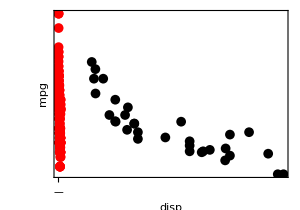

```mathematica
ggplot[dates,
	geomPoint["data"->mtcars,"x"->"disp","y"->"mpg"],
	geomPoint["data"->mpg,"x"->"displ","y"->"hwy","color"->Red]
]
```

```mathematica
s
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

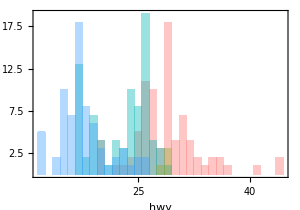

```mathematica
mpg//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[geomHistogram["x"->"hwy","color"->"cyl","alpha"->Opacity[0.4],"bspec"->{1}]]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

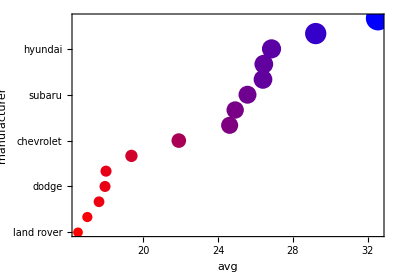

```mathematica
mpg//
	op[GroupBy[Function[#manufacturer]->Function[#hwy],Mean/*N]]//
	tidyExpression[{"manufacturer","avg"}]//
	SortBy[Last]//
	ggplot["y"->"manufacturer","x"->"avg","color"->"avg","size"->"avg",geomPoint[]]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

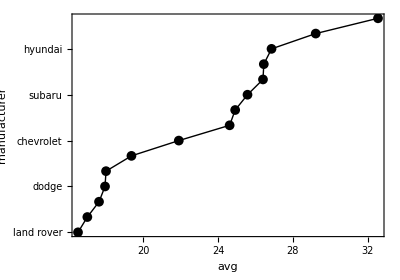

```mathematica
mpg//
	op[GroupBy[Function[#manufacturer]->Function[#hwy],Mean/*N]]//
	tidyExpression[{"manufacturer","avg"}]//
	SortBy[Last]//
	ggplot["y"->"manufacturer","x"->"avg",geomPoint[],geomLine[]]
```

xDiscreteLabels: {audi,chevrolet,dodge,ford,honda,hyundai,jeep,land rover,lincoln,mercury,nissan,pontiac,subaru,toyota,volkswagen}

xScaleType: Discrete

{{1,audi,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2,chevrolet,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3,dodge,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4,ford,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5,honda,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6,hyundai,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{7,jeep,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{8,land rover,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{9,lincoln,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{10,mercury,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{11,nissan,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{12,pontiac,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{13,subaru,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{14,toyota,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{15,volkswagen,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

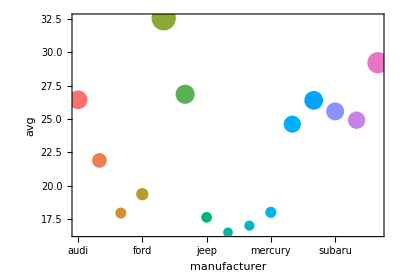

```mathematica
mpg//
	op[GroupBy[Function[#manufacturer]->Function[#hwy],Mean/*N]]//
	tidyExpression[{"manufacturer","avg"}]//
	ggplot["x"->"manufacturer","y"->"avg","size"->"avg","color"->"manufacturer",geomPoint[], geomLine[]]
```

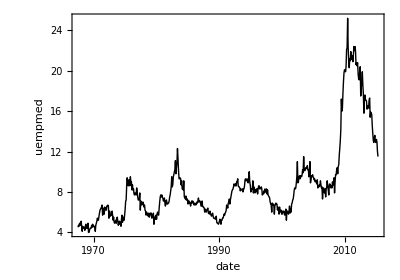

```mathematica
economics//
	ggplot[
		"x"->"date","y"->"uempmed",geomLine[],scaleXDate2[]
	]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{numberOfMajorTicks2→20,majorGridLineStyle2→RGBColor[1, 0, 0]}]

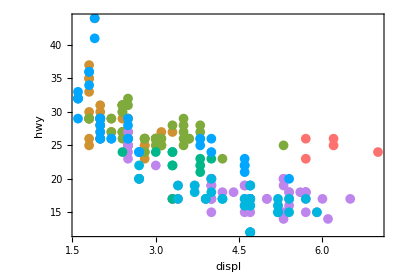

```mathematica
mpg//
	ggplot[geomPoint["x"->"displ","y"->"hwy","color"->"class"],numberOfMajorTicks2->20,majorGridLineStyle2->Red]
```

```mathematica
ticks2[]
```

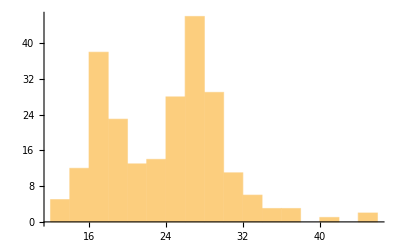

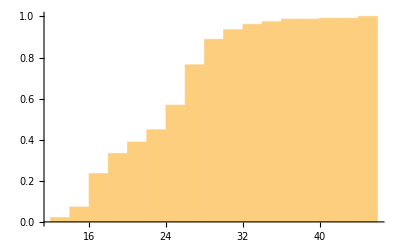

```mathematica
Histogram[mpg[[All,"hwy"]]]
Histogram[mpg[[All,"hwy"]],Automatic,"CDF"]
```

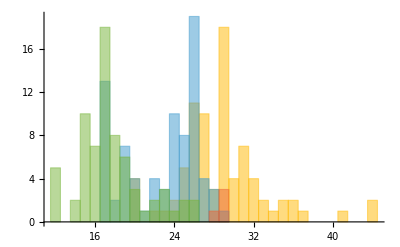

```mathematica
mpg//
	GroupBy[Function[#cyl]->Function[#hwy]]//
	op[Histogram[{1},PlotRange->All]]
```

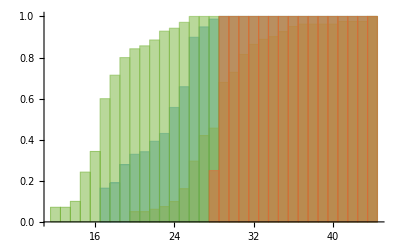

```mathematica
mpg//
	GroupBy[Function[#cyl]->Function[#hwy]]//
	op[Histogram[{1},"CDF",PlotRange->All]]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

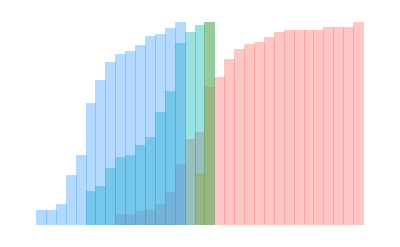

```mathematica
mpg//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[geomHistogram["x"->"hwy","color"->"cyl","alpha"->Opacity[0.4],"bspec"->{1},"hspec"->"CDF"]]
```

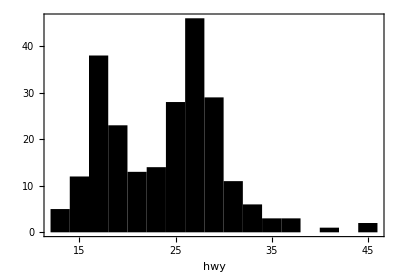

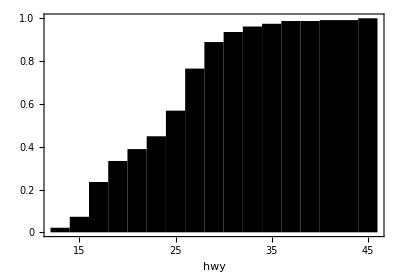

```mathematica
ggplot["data"->mpg,geomHistogram["x"->"hwy"]]
ggplot["data"->mpg,geomHistogram["x"->"hwy","hspec"->"CDF"]]
```

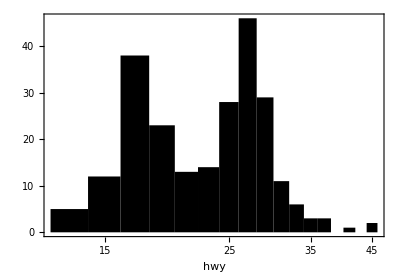

```mathematica
ggplot["data"->mpg,geomHistogram["x"->"hwy"],scaleXLog2[]]
```

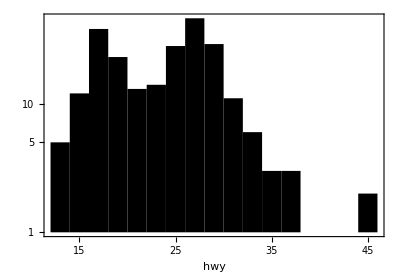

```mathematica
ggplot["data"->mpg,geomHistogram["x"->"hwy"],scaleYLog2[]]
```

xScaleType: Date

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Date,ggplot`Private`min,ggplot`Private`max,{}]

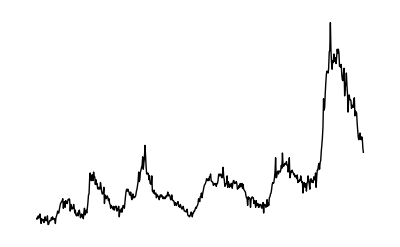

```mathematica
economics//
	ggplot[
		"x"->"date","y"->"uempmed",geomLine[],scaleXDate2[]
	]
```

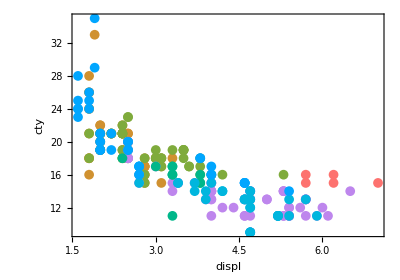

```mathematica
mpg//ggplot[geomPoint["x"->"displ","y"->"cty","color"->"class"]]
```

Need to be able to handle this kind of case

```mathematica
(*Need to be able to handle this kind of case*)
mtcars//ggplot[
	geomPoint["data"->mtcars,"x"->"disp","y"->"mpg"]
	];
```

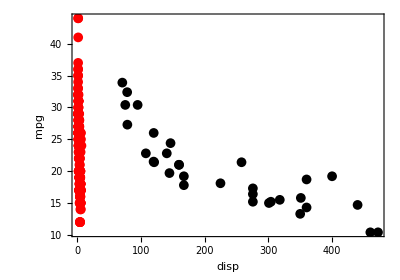

```mathematica
ggplot[mtcars,"x"->"disp","y"->"mpg",
	geomPoint[],
	geomPoint["data"->mpg,"x"->"displ","y"->"hwy","color"->Red]
]
```

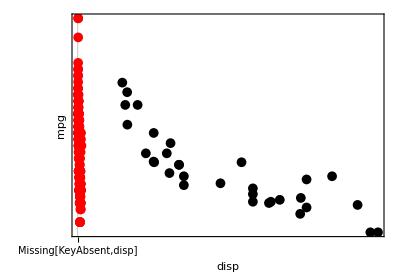

```mathematica
ggplot[dates,
	geomPoint["data"->mtcars,"x"->"disp","y"->"mpg"],
	geomPoint["data"->mpg,"x"->"displ","y"->"hwy","color"->Red]
]
```

```mathematica
ggplot[
geomPoint["data"->mtcars,"x"->"disp","y"->"mpg"],
geomPoint["data"->mpg,"x"->"displ","y"->"hwy","color"->Red]
]
```

-Graphics-

```mathematica
mtcars
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

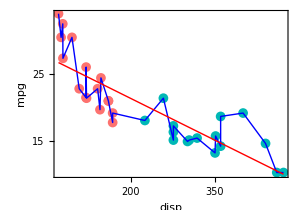

```mathematica
mtcars//
	ggplot["x"->"disp","y"->"mpg",geomPoint["color"->Function[#disp>200]],geomLine["color"->Blue],geomSmooth["color"->Red]]
```

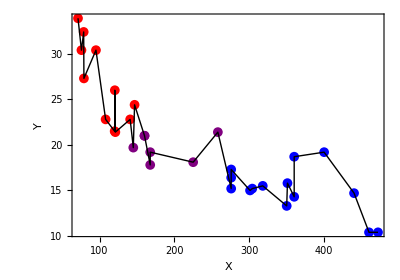

```mathematica
mtcars//
	ggplot[
		geomPoint["x"->"disp","y"->"mpg","color"->"cyl"],
		geomLine["x"->"disp","y"->"mpg","color"->Black]
	,FrameLabel->{"X","Y"}]
```

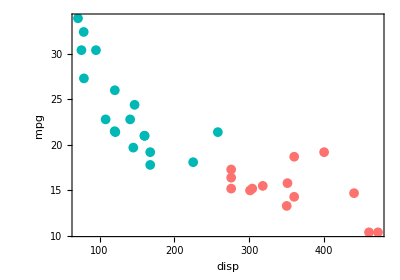

```mathematica
mtcars//ggplot[geomPoint["x"->"disp","y"->"mpg","color"->Function[#cyl<8]]]
```

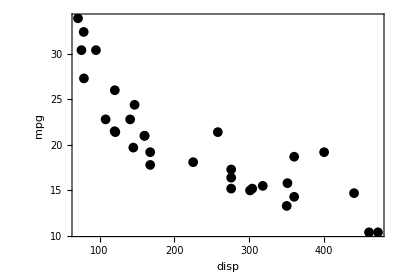

```mathematica
mtcars//ggplot[geomPoint["x"->"disp","y"->"mpg"]]
```

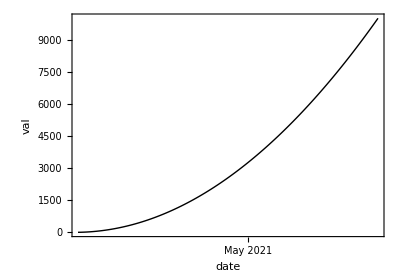

```mathematica
dates//
	ggplot[geomLine["x"->"date","y"->"val"],scaleXDate2[]]
```

```mathematica
mtcars//
	ggplot["x"->"disp","y"->"mpg",geomPoint[]]
```

-Graphics-

```mathematica
ggplot["data"->mtcars,"x"->"disp","y"->"mpg",geomPoint[]]
```

-Graphics-

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

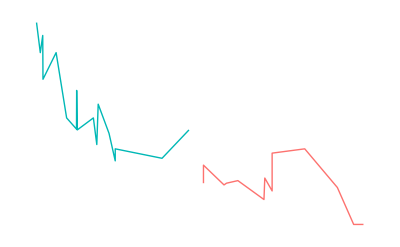

```mathematica
ggplot[
	geomLine["x"->"disp","y"->"mpg","color"->Function[#cyl<8]],
	geomParityLine["color"->Red,"alpha"->Opacity[0.2]],
	"data"->mtcars
]
```

```mathematica
ticks2["Linear", 0, 10, {}][[All, {1,2,3}]]
```

{{0,0,{0.,0.}},{2,2,{0.,0.}},{4,4,{0.,0.}},{6,6,{0.,0.}},{8,8,{0.,0.}},{10,10,{0.,0.}},{0.,,{0.,0.}},{0.5,,{0.,0.}},{1.,,{0.,0.}},{1.5,,{0.,0.}},{2.,,{0.,0.}},{2.5,,{0.,0.}},{3.,,{0.,0.}},{3.5,,{0.,0.}},{4.,,{0.,0.}},{4.5,,{0.,0.}},{5.,,{0.,0.}},{5.5,,{0.,0.}},{6.,,{0.,0.}},{6.5,,{0.,0.}},{7.,,{0.,0.}},{7.5,,{0.,0.}},{8.,,{0.,0.}},{8.5,,{0.,0.}},{9.,,{0.,0.}},{9.5,,{0.,0.}},{10.,,{0.,0.}}}

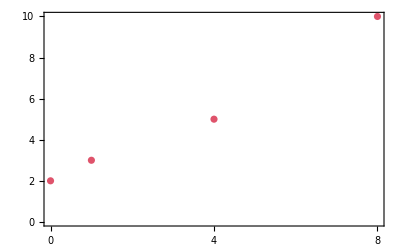

```mathematica
ListPlot[{{0,2}, {1,3}, {4,5}, {8,10}}, FrameTicks->{ticks2["Linear", 0, 10, {}],ticks2["Linear", 0, 10, {}]}]
```

```mathematica
ggplot["data"->mtcars,"x"->"disp","y"->"mpg",geomPoint[],geomLine[],scaleXLog2[]]
```

xScaleType: Log

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Log,ggplot`Private`min,ggplot`Private`max,{}]

-Graphics-

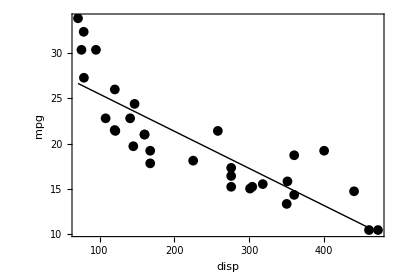

```mathematica
ggplot["data"->mtcars,"x"->"disp","y"->"mpg",geomPoint[],geomSmooth[]]
```

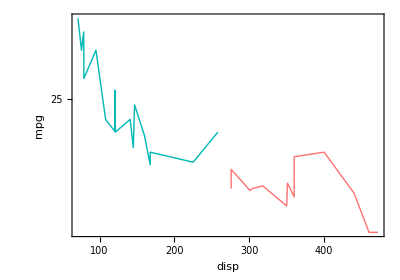

```mathematica
ggplot["data"->mtcars,
	geomLine["x"->"disp","y"->"mpg","color"->Function[#cyl<8]],
	geomParityLine["color"->Red,"alpha"->Opacity[0.2]]
]
```

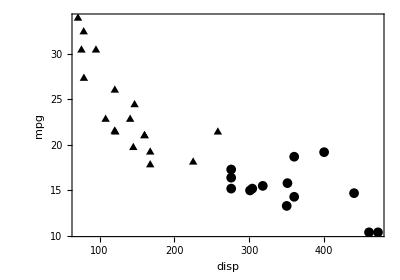

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","shape"->(*Null*)Function[#cyl<8]]]
```

```mathematica
mtcars//
	ggplot["x"->"disp","y"->"mpg",
	geomPoint[],
	geomSmooth[],
	scaleYLog2[],
	scaleXLog2[]
	]
```

-Graphics-

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"],geomSmooth["x"->"disp","y"->"mpg"],scaleYLog2[],scaleXLog2[]]
```

-Graphics-

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"],geomHLine["yIntercept"->10],geomVLine["xIntercept"->100],scaleYLog2[],scaleXLog2[]]
```

-Graphics-

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"]]
```

-Graphics-

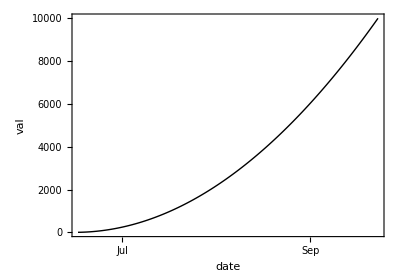

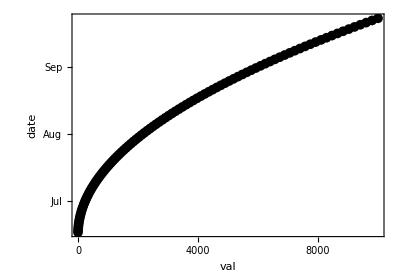

```mathematica
dates//
	ggplot[geomLine["x"->"date","y"->"val"],scaleXDate2[]]
dates//
	ggplot[geomPoint["y"->"date","x"->"val"],scaleYDate2[]]
```

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg"],geomSmooth["x"->"disp","y"->"mpg"]]
```

-Graphics-

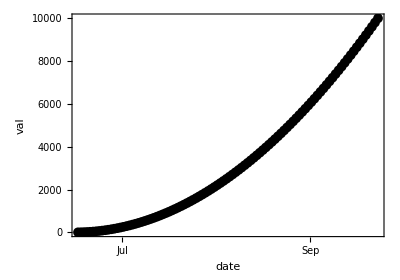

-Graphics-

```mathematica
dates//
	ggplot[geomPoint["x"->"date","y"->"val"],scaleXDate2[]]
dates//
	ggplot[geomPoint["x"->"val","y"->"date"],scaleYDate2[]]
```

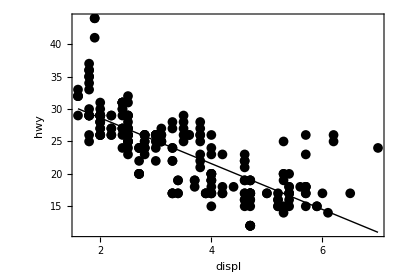

```mathematica
mpg//
	ggplot[
		geomPoint["x"->"displ","y"->"hwy"],
		geomSmooth["x"->"displ","y"->"hwy"]
	]
```

-Graphics-

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

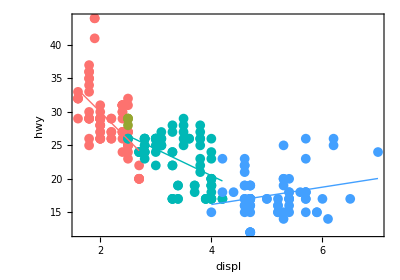

```mathematica
mpg//
	ggplot[
		geomPoint["x"->"displ","y"->"hwy"],
		geomSmooth["x"->"displ","y"->"hwy"]
	]
mpg//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[
		geomPoint["x"->"displ","y"->"hwy","color"->"cyl"],
		geomSmooth["x"->"displ","y"->"hwy","color"->"cyl"]
	]
```

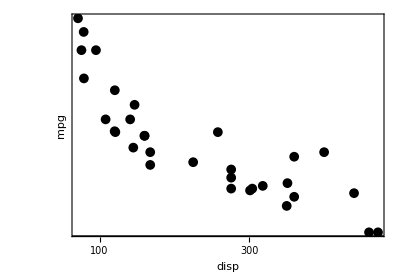

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"],geomParityLine[],geomHLine["yIntercept"->10],geomVLine["xIntercept"->10,"color"->Red]]
```

```mathematica
ggplot[mtcars,geomPoint["x"->"disp","y"->"mpg"]]
(*mtcars//ggplot[geomPoint["x"->"disp","y"->"mpg"]]*)
```

-Graphics-

```mathematica
mtcars//
	GroupBy[#cyl&]//
	Map[summarize[{"avg_mpg"->Function[Mean@#mpg],"avg_disp"->Function[Mean@#disp]}]]//
	Values//
	ggplot[geomPoint["y"->"avg_mpg","x"->"avg_disp"]]
```

ggplot[geomPoint[y→avg_mpg,x→avg_disp]][{summarize[{avg_mpg→(Mean[#mpg]&),avg_disp→(Mean[#disp]&)}][{<|mpg→21,cyl→6,disp→160,hp→110,drat→3.9,wt→2.62,qsec→16.46,vs→0,am→1,gear→4,carb→4|>,<|mpg→21,cyl→6,disp→160,hp→110,drat→3.9,wt→2.875,qsec→17.02,vs→0,am→1,gear→4,carb→4|>,<|mpg→21.4,cyl→6,disp→258,hp→110,drat→3.08,wt→3.215,qsec→19.44,vs→1,am→0,gear→3,carb→1|>,<|mpg→18.1,cyl→6,disp→225,hp→105,drat→2.76,wt→3.46,qsec→20.22,vs→1,am→0,gear→3,carb→1|>,<|mpg→19.2,cyl→6,disp→167.6,hp→123,drat→3.92,wt→3.44,qsec→18.3,vs→1,am→0,gear→4,carb→4|>,<|mpg→17.8,cyl→6,disp→167.6,hp→123,drat→3.92,wt→3.44,qsec→18.9,vs→1,am→0,gear→4,carb→4|>,<|mpg→19.7,cyl→6,disp→145,hp→175,drat→3.62,wt→2.77,qsec→15.5,vs→0,am→1,gear→5,carb→6|>}],summarize[{avg_mpg→(Mean[#mpg]&),avg_disp→(Mean[#disp]&)}][{<|mpg→22.8,cyl→4,disp→108,hp→93,drat→3.85,wt→2.32,qsec→18.61,vs→1,am→1,gear→4,carb→1|>,<|mpg→24.4,cyl→4,disp→146.7,hp→62,drat→3.69,wt→3.19,qsec→20,vs→1,am→0,gear→4,carb→2|>,<|mpg→22.8,cyl→4,disp→140.8,hp→95,drat→3.92,wt→3.15,qsec→22.9,vs→1,am→0,gear→4,carb→2|>,<|mpg→32.4,cyl→4,disp→78.7,hp→66,drat→4.08,wt→2.2,qsec→19.47,vs→1,am→1,gear→4,carb→1|>,<|mpg→30.4,cyl→4,disp→75.7,hp→52,drat→4.93,wt→1.615,qsec→18.52,vs→1,am→1,gear→4,carb→2|>,<|mpg→33.9,cyl→4,disp→71.1,hp→65,drat→4.22,wt→1.835,qsec→19.9,vs→1,am→1,gear→4,carb→1|>,<|mpg→21.5,cyl→4,disp→120.1,hp→97,drat→3.7,wt→2.465,qsec→20.01,vs→1,am→0,gear→3,carb→1|>,<|mpg→27.3,cyl→4,disp→79,hp→66,drat→4.08,wt→1.935,qsec→18.9,vs→1,am→1,gear→4,carb→1|>,<|mpg→26,cyl→4,disp→120.3,hp→91,drat→4.43,wt→2.14,qsec→16.7,vs→0,am→1,gear→5,carb→2|>,<|mpg→30.4,cyl→4,disp→95.1,hp→113,drat→3.77,wt→1.513,qsec→16.9,vs→1,am→1,gear→5,carb→2|>,<|mpg→21.4,cyl→4,disp→121,hp→109,drat→4.11,wt→2.78,qsec→18.6,vs→1,am→1,gear→4,carb→2|>}],summarize[{avg_mpg→(Mean[#mpg]&),avg_disp→(Mean[#disp]&)}][{<|mpg→18.7,cyl→8,disp→360,hp→175,drat→3.15,wt→3.44,qsec→17.02,vs→0,am→0,gear→3,carb→2|>,<|mpg→14.3,cyl→8,disp→360,hp→245,drat→3.21,wt→3.57,qsec→15.84,vs→0,am→0,gear→3,carb→4|>,<|mpg→16.4,cyl→8,disp→275.8,hp→180,drat→3.07,wt→4.07,qsec→17.4,vs→0,am→0,gear→3,carb→3|>,<|mpg→17.3,cyl→8,disp→275.8,hp→180,drat→3.07,wt→3.73,qsec→17.6,vs→0,am→0,gear→3,carb→3|>,<|mpg→15.2,cyl→8,disp→275.8,hp→180,drat→3.07,wt→3.78,qsec→18,vs→0,am→0,gear→3,carb→3|>,<|mpg→10.4,cyl→8,disp→472,hp→205,drat→2.93,wt→5.25,qsec→17.98,vs→0,am→0,gear→3,carb→4|>,<|mpg→10.4,cyl→8,disp→460,hp→215,drat→3,wt→5.424,qsec→17.82,vs→0,am→0,gear→3,carb→4|>,<|mpg→14.7,cyl→8,disp→440,hp→230,drat→3.23,wt→5.345,qsec→17.42,vs→0,am→0,gear→3,carb→4|>,<|mpg→15.5,cyl→8,disp→318,hp→150,drat→2.76,wt→3.52,qsec→16.87,vs→0,am→0,gear→3,carb→2|>,<|mpg→15.2,cyl→8,disp→304,hp→150,drat→3.15,wt→3.435,qsec→17.3,vs→0,am→0,gear→3,carb→2|>,<|mpg→13.3,cyl→8,disp→350,hp→245,drat→3.73,wt→3.84,qsec→15.41,vs→0,am→0,gear→3,carb→4|>,<|mpg→19.2,cyl→8,disp→400,hp→175,drat→3.08,wt→3.845,qsec→17.05,vs→0,am→0,gear→3,carb→2|>,<|mpg→15.8,cyl→8,disp→351,hp→264,drat→4.22,wt→3.17,qsec→14.5,vs→0,am→1,gear→5,carb→4|>,<|mpg→15,cyl→8,disp→301,hp→335,drat→3.54,wt→3.57,qsec→14.6,vs→0,am→1,gear→5,carb→8|>}]}]

```mathematica
(*Takes a long time*)
(*diamonds//
	ggplot[geomPoint["x"->"carat","y"->"price","alpha"->Opacity[0.02]]]*)
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

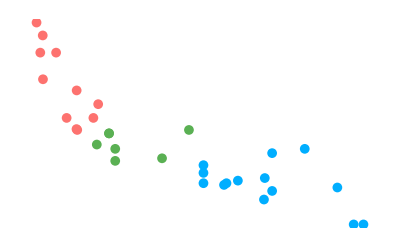

```mathematica
mtcars//
	MapAt[ToString,{{All,"cyl"},{All,"gear"}}]//
	ggplot[geomPoint["x"->"disp","y"->"mpg","color"->"cyl"]]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

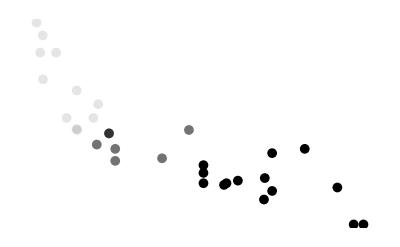

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","alpha"->"cyl"]]
```

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

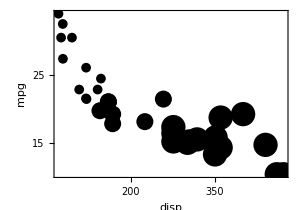

```mathematica
mtcars//
	ggplot[geomPoint["x"->"disp","y"->"mpg","size"->"cyl"]]
```

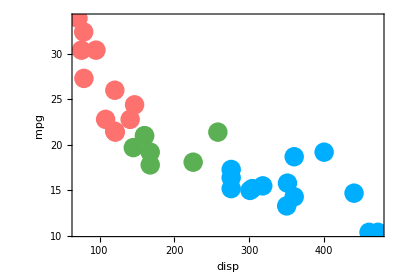

```mathematica
mtcars//
	MapAt[ToString,{All,"cyl"}]//
	ggplot[geomPoint["x"->"disp","y"->"mpg","color"->"cyl","size"->20]]
```

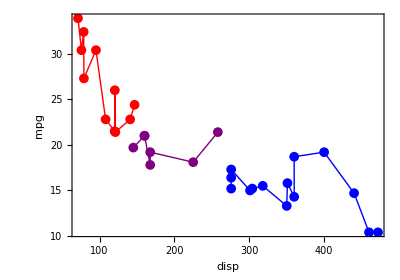

```mathematica
mtcars//
	ggplot[
		geomPoint["x"->"disp","y"->"mpg","color"->"cyl"],
		geomLine["x"->"disp","y"->"mpg","color"->"cyl"]
	]
```

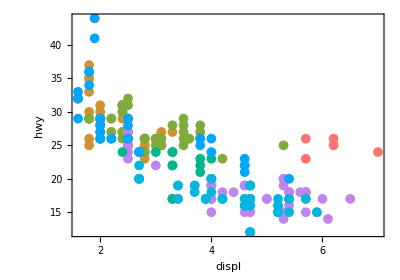

```mathematica
mpg//
	ggplot[geomPoint["x"->"displ","y"->"hwy","color"->"class"]]
```

Columns

```mathematica
(*mpg//
	ggplot[geomCol["x"->"displ","y"->"hwy"]]*)
```

#### Testing: Tick

Tick (and gridline) functionality needs to support a wide range of capabilities including:

Classic linear ticks2
Date ticks2
Log (Log/Log10/Log2) ticks2
Discrete ticks2 (which would be for labels like “a”, “b”, ... “z”)

xScaleType: Linear

min: ggplot`Private`min

max: ggplot`Private`max

ticks2[Linear,ggplot`Private`min,ggplot`Private`max,{}]

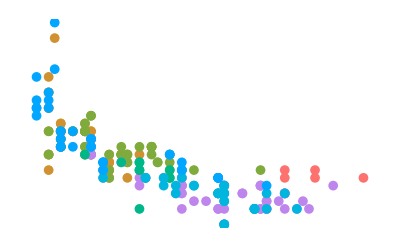

```mathematica
mpg//ggplot[geomPoint["x"->"displ","y"->"cty","color"->"class"]]
```

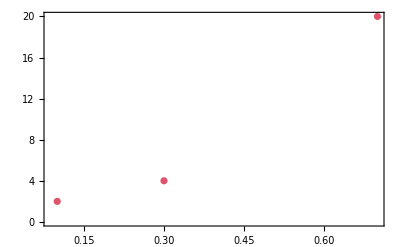

```mathematica
ListPlot[{{0.1,2}, {0.3,4}, {0.7,20}}, Ticks->t]
```

```mathematica
t
```

```mathematica
t = ticks2["Linear",0,1,numberOfMinorTicksPerMajorTick2->2]
gridLines2["Linear",0,1,numberOfMinorTicksPerMajorTick2->2]
```

{{0,0,{0.03,0.},Directive[GrayLevel[0],Thickness[0.01]]},{1/5,0.2,{0.03,0.},Directive[GrayLevel[0],Thickness[0.01]]},{2/5,0.4,{0.03,0.},Directive[GrayLevel[0],Thickness[0.01]]},{3/5,0.6,{0.03,0.},Directive[GrayLevel[0],Thickness[0.01]]},{4/5,0.8,{0.03,0.},Directive[GrayLevel[0],Thickness[0.01]]},{1,1.0,{0.03,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.05,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.1,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.15,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.2,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.25,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.3,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.35,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.4,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.45,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.5,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.55,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.6,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.65,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.7,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.75,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.8,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.85,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.9,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{0.95,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]},{1.,,{0.012,0.},Directive[GrayLevel[0],Thickness[0.01]]}}

{{0,Directive[GrayLevel[0.8],Thickness[0.002]]},{1/5,Directive[GrayLevel[0.8],Thickness[0.002]]},{2/5,Directive[GrayLevel[0.8],Thickness[0.002]]},{3/5,Directive[GrayLevel[0.8],Thickness[0.002]]},{4/5,Directive[GrayLevel[0.8],Thickness[0.002]]},{1,Directive[GrayLevel[0.8],Thickness[0.002]]},{0.,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.05,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.1,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.15,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.2,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.25,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.3,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.35,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.4,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.45,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.5,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.55,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.6,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.65,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.7,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.75,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.8,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.85,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.9,Directive[GrayLevel[0.9],Thickness[0.001]]},{0.95,Directive[GrayLevel[0.9],Thickness[0.001]]},{1.,Directive[GrayLevel[0.9],Thickness[0.001]]}}

```mathematica
ticks2["Linear",0,1,numberOfMinorTicksPerMajorTick2->2]
gridLines2["Linear",0,1,numberOfMinorTicksPerMajorTick2->2]
```

{{0.,0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.2,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.4,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.6,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.8,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.1,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.3,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.5,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.7,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.9,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

{{0.,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.2,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.4,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.6,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.8,Directive[GrayLevel[0.6],Thickness[0.0008]]},{1.,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.1,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.3,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.5,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.7,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.9,Directive[GrayLevel[0.85],Thickness[0.0008]]}}

```mathematica
ticks2["Date",Now,Now+Quantity[1,"Years"]]
gridLines2["Date",Now,Now+Quantity[1,"Years"]]
```

{{3.78683×10^9,Jan,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.79469×10^9,Apr,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.80255×10^9,Jul,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.8105×10^9,Oct,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.81845×10^9,Jan,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.82622×10^9,Apr,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.83409×10^9,Jul,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.84204×10^9,Oct,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

{{3.78683×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3.79469×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3.80255×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3.8105×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3.81845×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3.82622×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3.83409×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3.84204×10^9,Directive[GrayLevel[0.6],Thickness[0.0008]]}}

```mathematica
t=ticks2["Log",0,1,numberOfMinorTicksPerMajorTick2->1]
g=gridLines2["Log",0,1,numberOfMinorTicksPerMajorTick2->1]
```

{{0.,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.182322,1.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.405465,1.5,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.587787,1.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.693147,2.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.788457,2.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.916291,2.5,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.09861,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

{{0.,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.182322,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.405465,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.587787,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.693147,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.788457,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.916291,Directive[GrayLevel[0.6],Thickness[0.0008]]},{1.09861,Directive[GrayLevel[0.85],Thickness[0.0008]]}}

```mathematica
ticks2["Linear",0,1,numberOfMinorTicksPerMajorTick2->3]
gridLines2["Linear",0,1,numberOfMinorTicksPerMajorTick2->3]
```

{{0,0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1/5,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2/5,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3/5,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4/5,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.05,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.1,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.15,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.3,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.35,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.4,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.45,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.5,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.55,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.6,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.65,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.7,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.75,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.8,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.85,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.9,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.95,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

{{0,Directive[GrayLevel[0.6],Thickness[0.0008]]},{1/5,Directive[GrayLevel[0.6],Thickness[0.0008]]},{2/5,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3/5,Directive[GrayLevel[0.6],Thickness[0.0008]]},{4/5,Directive[GrayLevel[0.6],Thickness[0.0008]]},{1,Directive[GrayLevel[0.6],Thickness[0.0008]]},{0.,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.05,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.1,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.15,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.2,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.25,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.3,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.35,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.4,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.45,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.5,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.55,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.6,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.65,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.7,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.75,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.8,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.85,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.9,Directive[GrayLevel[0.85],Thickness[0.0008]]},{0.95,Directive[GrayLevel[0.85],Thickness[0.0008]]},{1.,Directive[GrayLevel[0.85],Thickness[0.0008]]}}

```mathematica
ListPlot[{}, Ticks->t]
```

-Graphics-

```mathematica
ggplotSetTheme[ggPlot]
```

```mathematica
ggplotSetTheme[ggPlotThemePub]
```

ggplotSetTheme[ggPlotThemePub]

```mathematica
ggplotSetTheme[ggplotThemePub]
```

ggplotSetTheme[ggplotThemePub]

```mathematica
t=ticks2["Discrete",{"a","b","c","d","e"},numberOfMinorTicksPerMajorTick2->2]
```

{{1,a,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2,b,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3,c,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4,d,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5,e,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{7/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{9/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
t=ticks2["Discrete",{"a","b","c","d","e"},numberOfMinorTicksPerMajorTick2->2, numberOfMajorTicks2->2]
g=gridLines2["Discrete",{"a","b","c","d","e"},numberOfMinorTicksPerMajorTick2->2]
```

{{1,a,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2,b,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3,c,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4,d,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5,e,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{7/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{9/2,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

{{1,Directive[GrayLevel[0.6],Thickness[0.0008]]},{2,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3,Directive[GrayLevel[0.6],Thickness[0.0008]]},{4,Directive[GrayLevel[0.6],Thickness[0.0008]]},{5,Directive[GrayLevel[0.6],Thickness[0.0008]]},{3/2,Directive[GrayLevel[0.85],Thickness[0.0008]]},{5/2,Directive[GrayLevel[0.85],Thickness[0.0008]]},{7/2,Directive[GrayLevel[0.85],Thickness[0.0008]]},{9/2,Directive[GrayLevel[0.85],Thickness[0.0008]]}}

```mathematica
Ticks
```

```mathematica
GetTickMarks[{{0,10}, {0,10}}]
```

{{{{0.,0,{0.03,0}},{2.,2,{0.03,0}},{4.,4,{0.03,0}},{6.,6,{0.03,0}},{8.,8,{0.03,0}},{10.,10,{0.03,0}},{-1.5,Null,{0.012,0}},{-1.,Null,{0.012,0}},{-0.5,Null,{0.012,0}},{0.5,Null,{0.012,0}},{1.,Null,{0.012,0}},{1.5,Null,{0.012,0}},{2.5,Null,{0.012,0}},{3.,Null,{0.012,0}},{3.5,Null,{0.012,0}},{4.5,Null,{0.012,0}},{5.,Null,{0.012,0}},{5.5,Null,{0.012,0}},{6.5,Null,{0.012,0}},{7.,Null,{0.012,0}},{7.5,Null,{0.012,0}},{8.5,Null,{0.012,0}},{9.,Null,{0.012,0}},{9.5,Null,{0.012,0}},{10.5,Null,{0.012,0}},{11.,Null,{0.012,0}},{11.5,Null,{0.012,0}}},{{0.,Null,{0.03,0}},{2.,Null,{0.03,0}},{4.,Null,{0.03,0}},{6.,Null,{0.03,0}},{8.,Null,{0.03,0}},{10.,Null,{0.03,0}},{-1.5,Null,{0.012,0}},{-1.,Null,{0.012,0}},{-0.5,Null,{0.012,0}},{0.5,Null,{0.012,0}},{1.,Null,{0.012,0}},{1.5,Null,{0.012,0}},{2.5,Null,{0.012,0}},{3.,Null,{0.012,0}},{3.5,Null,{0.012,0}},{4.5,Null,{0.012,0}},{5.,Null,{0.012,0}},{5.5,Null,{0.012,0}},{6.5,Null,{0.012,0}},{7.,Null,{0.012,0}},{7.5,Null,{0.012,0}},{8.5,Null,{0.012,0}},{9.,Null,{0.012,0}},{9.5,Null,{0.012,0}},{10.5,Null,{0.012,0}},{11.,Null,{0.012,0}},{11.5,Null,{0.012,0}}}},{{{0.,0,{0.03,0}},{2.,2,{0.03,0}},{4.,4,{0.03,0}},{6.,6,{0.03,0}},{8.,8,{0.03,0}},{10.,10,{0.03,0}},{-1.5,Null,{0.012,0}},{-1.,Null,{0.012,0}},{-0.5,Null,{0.012,0}},{0.5,Null,{0.012,0}},{1.,Null,{0.012,0}},{1.5,Null,{0.012,0}},{2.5,Null,{0.012,0}},{3.,Null,{0.012,0}},{3.5,Null,{0.012,0}},{4.5,Null,{0.012,0}},{5.,Null,{0.012,0}},{5.5,Null,{0.012,0}},{6.5,Null,{0.012,0}},{7.,Null,{0.012,0}},{7.5,Null,{0.012,0}},{8.5,Null,{0.012,0}},{9.,Null,{0.012,0}},{9.5,Null,{0.012,0}},{10.5,Null,{0.012,0}},{11.,Null,{0.012,0}},{11.5,Null,{0.012,0}}},{{0.,Null,{0.03,0}},{2.,Null,{0.03,0}},{4.,Null,{0.03,0}},{6.,Null,{0.03,0}},{8.,Null,{0.03,0}},{10.,Null,{0.03,0}},{-1.5,Null,{0.012,0}},{-1.,Null,{0.012,0}},{-0.5,Null,{0.012,0}},{0.5,Null,{0.012,0}},{1.,Null,{0.012,0}},{1.5,Null,{0.012,0}},{2.5,Null,{0.012,0}},{3.,Null,{0.012,0}},{3.5,Null,{0.012,0}},{4.5,Null,{0.012,0}},{5.,Null,{0.012,0}},{5.5,Null,{0.012,0}},{6.5,Null,{0.012,0}},{7.,Null,{0.012,0}},{7.5,Null,{0.012,0}},{8.5,Null,{0.012,0}},{9.,Null,{0.012,0}},{9.5,Null,{0.012,0}},{10.5,Null,{0.012,0}},{11.,Null,{0.012,0}},{11.5,Null,{0.012,0}}}}}

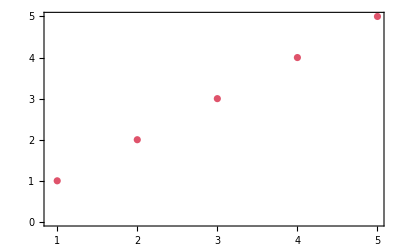

```mathematica
ListPlot[Range[5],Ticks->{t,Automatic},GridLines->{g,None}]
```

#### Testing: Theme

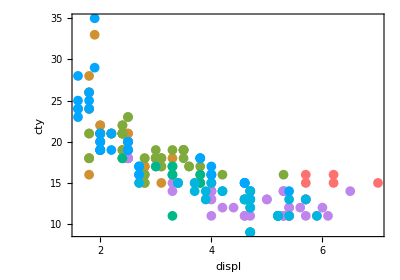

```mathematica
ggplot[mpg,geomPoint["x"->"displ","y"->"cty","color"->"class"]]
```

```mathematica
ggplotSetTheme[ggplotThemeGray];
```

```mathematica
ggplotSetTheme[ggplotThemeWhite]
```

```mathematica
Graphics[{RGBColor[0.92,0.92,0.92,1.],Rectangle[Scaled[{0,0}],Scaled[{1,1}]],Black,Point[{{0,0},{0.5,0.5},{0.6,0.6},{1,1}}]},gridLines2->Function[{min,max},gridLines2["Linear",min,max]],Frame->True,Axes->False,Method->{"GridLinesInFront"->True}]
```

-Graphics-

```mathematica
ggplot[mpg,geomPoint["x"->"displ","y"->"cty","color"->"class"]]
```

-Graphics-

#### Development: Faster ability to put Points in a Graphics object

GeometricTransformation can be used to take a single Inset command and replicate it at multiple locations

```mathematica
Graphics[{Red,Point[{{0,0},{1,1}}],
Blue,GeometricTransformation[Inset["A",{0,0}],{{{0.5,0.5}},{{1,1}}}]
}]
```

-Graphics-

```mathematica
GeometricTransformation[Inset[Style[■,Rule[GraphicsBoxOptions,List[Rule[DefaultBaseStyle,Directive[PointSize[0.012833333333333334],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]]]]],List[0.,0.]],List[List[List[0.,0.]],List[List[1.,1.]]]]//InputForm
```

GeometricTransformation[
 Inset[Style[■, GraphicsBoxOptions -> 
    {DefaultBaseStyle -> Directive[PointSize[0.012833333333333334], 
       RGBColor[0.368417, 0.506779, 0.709798], AbsoluteThickness[1.6]]}], {0., 0.}], 
 {{{0., 0.}}, {{1., 1.}}}]

```mathematica
GeometricTransformation
```

```mathematica
ListPlot[{{0,0},{1,1}},PlotMarkers->■]//FullForm
```

Graphics[List[List[],List[List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],GeometricTransformation[Inset[Style[\[FilledSquare],Rule[GraphicsBoxOptions,List[Rule[DefaultBaseStyle,Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]]]]],List[0.,0.]],List[List[List[0.,0.]],List[List[1.,1.]]]]]],List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]],List[]],List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]]],List[]]],List[List[],List[]]],List[Rule[DisplayFunction,Identity],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[gridLines2,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["OptimizePlotMarkers",True],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Function[Identity[Slot[1]]][Part[Slot[1],1]],Function[Identity[Slot[1]]][Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0,1.],List[0,1.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.05]]]],Rule[ticks2,List[Automatic,Automatic]]]]

#### Development: Experimenting with coordinate and scale transforms

```mathematica
CoordinateTransform
```

```mathematica
ScalingTransform
```

```mathematica
x=RandomReal[{0,5000},{50,2}];
```

```mathematica
x
```

{{604.171,4678.13},{4528.04,4122.09},{7.12955,1352.87},{330.54,3741.},{1469.86,4414.34},{3728.29,2118.73},{175.051,1713.45},{4919.55,1013.24},{599.704,3787.8},{121.324,1792.87},{1063.68,4252.83},{4416.05,994.689},{296.035,4191.6},{4120.3,2512.06},{460.032,1519.86},{1506.73,2746.93},{1583.73,2201.3},{2324.68,2320.97},{2076.42,1904.64},{2509.8,3217.77},{4212.48,4150.62},{1968.64,1201.02},{2682.81,3814.99},{1628.31,3501.14},{4295.5,3377.52},{3408.8,962.72},{525.472,4568.01},{1717.95,4262.07},{4083.71,1932.62},{738.089,1586.93},{4502.78,1152.24},{4115.67,3221.26},{4567.6,106.174},{4590.74,4758.66},{2049.37,983.114},{2020.03,567.755},{4154.25,3938.77},{3614.72,2139.85},{4304.07,1152.22},{3728.62,1717.07},{3198.51,1552.09},{2878.99,4211.34},{1125.5,2040.74},{4199.72,3613.65},{1279.27,3942.59},{2189.7,2643.27},{3079.04,877.378},{3303.25,3211.64},{1615.54,1005.53},{352.108,3241.52}}

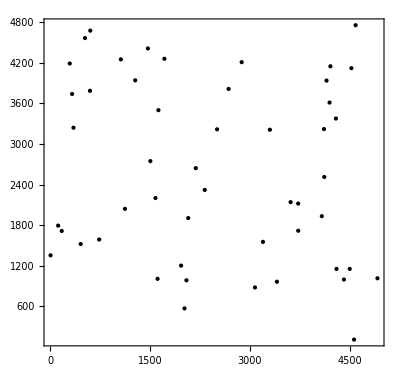

```mathematica
Graphics[Point@x,Frame->True,ScalingFunctions->"Log"]
```

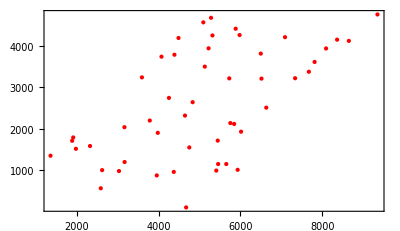

```mathematica
Graphics[GeometricTransformation[{Red,Point@x},ShearingTransform[Pi/4,{1,0},{0,1}]],Frame->True]
```

```mathematica
graphicsPrimitives=geomPoint[mtcars,"x"->"disp","y"->"mpg"]
```

{{GrayLevel[0],Opacity[1],GeometricTransformation[Inset[●,{0,0}],{{{160,21}},{{160,21}},{{108,22.8}},{{258,21.4}},{{360,18.7}},{{225,18.1}},{{360,14.3}},{{146.7,24.4}},{{140.8,22.8}},{{167.6,19.2}},{{167.6,17.8}},{{275.8,16.4}},{{275.8,17.3}},{{275.8,15.2}},{{472,10.4}},{{460,10.4}},{{440,14.7}},{{78.7,32.4}},{{75.7,30.4}},{{71.1,33.9}},{{120.1,21.5}},{{318,15.5}},{{304,15.2}},{{350,13.3}},{{400,19.2}},{{79,27.3}},{{120.3,26}},{{95.1,30.4}},{{351,15.8}},{{145,19.7}},{{301,15}},{{121,21.4}}}]}}

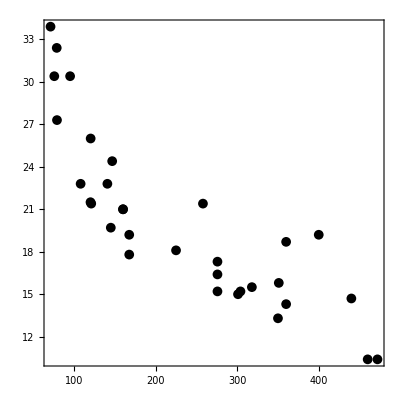

```mathematica
Graphics[graphicsPrimitives,Frame->True,AspectRatio->1]
```

```mathematica
Names["Charting`*ticks2*"]
```

{Charting`CategoricalTicksFunction,Charting`ComputeScaledTicks,Charting`convertTicks,Charting`DateTicksFunction,Charting`EvaluateTicksFunction,Charting`FindLogTicks,Charting`FindScaledTicks,Charting`FindTicks,Charting`FindTicksP,Charting`getDateTicks,Charting`PeriodicFrameTicks,Charting`PeriodicTicks,Charting`RotateTicks,Charting`SafeTicksFunctionQ,Charting`ScaledFrameTicks,Charting`ScaledTicks,Charting`ScaledTicks2,Charting`SimpleTicks,Charting`TicksFunction,Charting`unitTicksOnBar}

```mathematica
Names["Charting`*Date*"]
```

{Charting`adjustDateRange,Charting`DateAxis,Charting`DateDataParser,Charting`DateHeatmap,Charting`DatePlotParser,Charting`DateScale,Charting`DateScope,Charting`DateSpan,Charting`DateTicksFunction,Charting`DateValueParser,Charting`FindDateDivisions,Charting`fixDateGridLines,Charting`getDateTicks,Charting`iDateHeatmap,Charting`iDateHistogram,Charting`iDateListPlot,Charting`nearestDate}

```mathematica
Charting`FindDateDivisions[{Now,Now+Quantity[5,"Days"]},10]
Charting`FindDateDivisions[{AbsoluteTime@Now,AbsoluteTime[Now+Quantity[5,"Days"]]},10]
```

{{3.79719×10^9,Apr 30},{3.79728×10^9,May 01},{3.79737×10^9,May 02},{3.79745×10^9,May 03},{3.79754×10^9,May 04},{3.79763×10^9,May 05},{3.79771×10^9,May 06}}

{{3.79719×10^9,Apr 30},{3.79728×10^9,May 01},{3.79737×10^9,May 02},{3.79745×10^9,May 03},{3.79754×10^9,May 04},{3.79763×10^9,May 05},{3.79771×10^9,May 06}}

```mathematica
Charting`DateTicksFunction[{Now,Now+Quantity[5,"Days"]}]
```

Charting`DateTicksFunction[{Wed 29 Apr 2020 20:57:07GMT-5.,Mon 4 May 2020 20:57:07GMT-5.},DateTicksFormat→{Automatic}]

```mathematica
Charting`DateTicksFunction[{DateObject@Now,DateObject[Now+Quantity[5,"Days"]]},10]
```

Charting`DateTicksFunction[{Thu 30 Apr 2020 07:11:29GMT-5.,Tue 5 May 2020 07:11:29GMT-5.},10]

```mathematica
Options[Charting`DateTicksFunction]
```

{Alignment→Center,DateTicksFormat→Automatic,Exclusions→None,LabelingFunction→Automatic,Charting`LabelSide→Automatic,LabelStyle→{},Method→Automatic,Charting`PadLabels→Automatic,RotateLabel→Automatic,SaveDefinitions→False,ScalingFunctions→None,Charting`TickAnnotations→None,Charting`TickLabels→Automatic,Charting`TickLengths→Automatic,Charting`TickLevels→None,Charting`TickSide→Automatic,ticks2→None,TicksStyle→{},Charting`TickTemplate→None,Charting`TickWrappers→None}

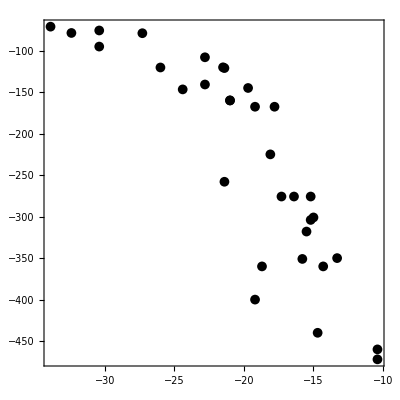

```mathematica
Graphics[GeometricTransformation[{Red,graphicsPrimitives},ReflectionTransform[{-1,-1}]],Frame->True,AspectRatio->1]
```

```mathematica
AffineTransform
```

```mathematica
mm=x//Transpose//Map[MinMax]
```

{{29.3241,995.013},{13.6287,977.428}}

```mathematica
x
```

{{891.065,236.666},{129.443,249.304},{753.784,589.46},{422.576,99.313},{390.227,343.934},{761.803,672.929},{412.919,685.539},{446.171,580.031},{662.715,438.062},{149.006,13.6287},{942.873,349.81},{345.488,74.7991},{724.946,685.394},{415.999,186.881},{773.869,806.993},{259.358,977.428},{122.164,191.762},{165.656,350.598},{266.201,861.733},{429.951,845.209},{76.8374,586.739},{297.405,797.065},{651.7,255.235},{372.917,747.532},{447.077,169.009},{947.698,602.575},{543.13,610.535},{995.013,803.896},{161.204,634.796},{35.8477,728.94},{900.601,45.0862},{590.924,289.473},{917.634,52.8401},{497.155,59.1239},{647.458,66.6291},{947.831,129.301},{944.796,945.299},{251.773,366.042},{957.772,52.019},{438.135,131.635},{442.838,471.548},{540.562,106.746},{29.3241,226.193},{504.522,254.124},{245.113,951.082},{463.581,260.814},{181.874,222.688},{550.566,441.65},{698.047,591.732},{208.279,432.103}}

```mathematica
blah=Flatten[{{{160,21}},{{160,21}},{{108,22.8}},{{258,21.4}},{{360,18.7}},{{225,18.1}},{{360,14.3}},{{146.7,24.4}},{{140.8,22.8}},{{167.6,19.2}},{{167.6,17.8}},{{275.8,16.4}},{{275.8,17.3}},{{275.8,15.2}},{{472,10.4}},{{460,10.4}},{{440,14.7}},{{78.7,32.4}},{{75.7,30.4}},{{71.1,33.9}},{{120.1,21.5}},{{318,15.5}},{{304,15.2}},{{350,13.3}},{{400,19.2}},{{79,27.3}},{{120.3,26}},{{95.1,30.4}},{{351,15.8}},{{145,19.7}},{{301,15}},{{121,21.4}}},1];
```

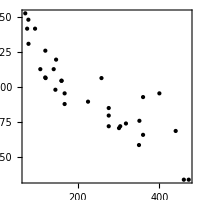

```mathematica
Graphics[Point@MapAt[Log,blah,{All,2}],Frame->True,ImageSize->200,AspectRatio->1]
```

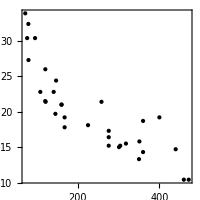

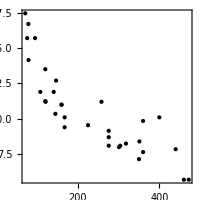

```mathematica
Graphics[Point@blah,Frame->True,ImageSize->200,AspectRatio->1]
Graphics[GeometricTransformation[Point@blah,RescalingTransform[{{-1,1},{-1,1}},{{-1,1},{0,1}}]],Frame->True,ImageSize->200,AspectRatio->1]
```

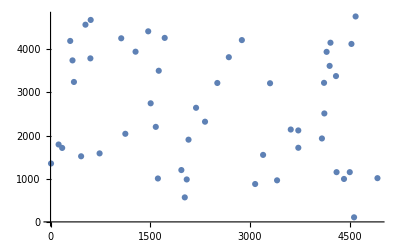

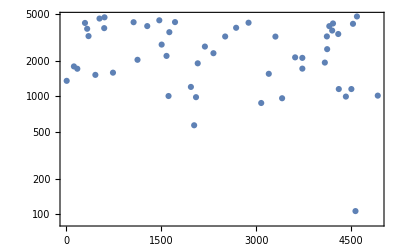

```mathematica
ListPlot[x]
ListPlot[x,ScalingFunctions->"Log",Frame->True]
```

```mathematica
ticks2=Charting`ScaledTicks[{Log, Exp}][1,100,{6,6}]
```

{{2.30259,10,{0.01,0.}},{25.3284,10^11,{0.01,0.}},{48.3543,10^21,{0.01,0.}},{71.3801,10^31,{0.01,0.}},{94.406,10^41,{0.01,0.}},{6.90776,,{0.005,0.}},{11.5129,,{0.005,0.}},{16.1181,,{0.005,0.}},{20.7233,,{0.005,0.}},{29.9336,,{0.005,0.}},{34.5388,,{0.005,0.}},{39.1439,,{0.005,0.}},{43.7491,,{0.005,0.}},{52.9595,,{0.005,0.}},{57.5646,,{0.005,0.}},{62.1698,,{0.005,0.}},{66.775,,{0.005,0.}},{75.9853,,{0.005,0.}},{80.5905,,{0.005,0.}},{85.1956,,{0.005,0.}},{89.8008,,{0.005,0.}},{99.0112,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks[{Log,Exp}][Log[1^2],Log[10^2],{6,6}]
```

{{0.,1,{0.01,0.}},{1.60944,5,{0.01,0.}},{2.30259,10,{0.01,0.}},{3.91202,50,{0.01,0.}},{4.60517,100,{0.01,0.}},{-0.693147,,{0.005,0.}},{-0.510826,,{0.005,0.}},{-0.356675,,{0.005,0.}},{-0.223144,,{0.005,0.}},{-0.105361,,{0.005,0.}},{0.693147,,{0.005,0.}},{1.09861,,{0.005,0.}},{1.38629,,{0.005,0.}},{1.79176,,{0.005,0.}},{1.94591,,{0.005,0.}},{2.07944,,{0.005,0.}},{2.19722,,{0.005,0.}},{2.99573,,{0.005,0.}},{3.4012,,{0.005,0.}},{3.68888,,{0.005,0.}},{4.09434,,{0.005,0.}},{4.2485,,{0.005,0.}},{4.38203,,{0.005,0.}},{4.49981,,{0.005,0.}},{5.29832,,{0.005,0.}},{5.70378,,{0.005,0.}},{5.99146,,{0.005,0.}},{6.21461,,{0.005,0.}},{6.39693,,{0.005,0.}},{6.55108,,{0.005,0.}},{6.68461,,{0.005,0.}},{6.80239,,{0.005,0.}},{6.90776,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks["Log"][Log[1^2],Log[10^2],{6,6}]
```

{{0.,1,{0.01,0.}},{1.60944,5,{0.01,0.}},{2.30259,10,{0.01,0.}},{3.91202,50,{0.01,0.}},{4.60517,100,{0.01,0.}},{-0.693147,,{0.005,0.}},{-0.510826,,{0.005,0.}},{-0.356675,,{0.005,0.}},{-0.223144,,{0.005,0.}},{-0.105361,,{0.005,0.}},{0.693147,,{0.005,0.}},{1.09861,,{0.005,0.}},{1.38629,,{0.005,0.}},{1.79176,,{0.005,0.}},{1.94591,,{0.005,0.}},{2.07944,,{0.005,0.}},{2.19722,,{0.005,0.}},{2.99573,,{0.005,0.}},{3.4012,,{0.005,0.}},{3.68888,,{0.005,0.}},{4.09434,,{0.005,0.}},{4.2485,,{0.005,0.}},{4.38203,,{0.005,0.}},{4.49981,,{0.005,0.}},{5.29832,,{0.005,0.}},{5.70378,,{0.005,0.}},{5.99146,,{0.005,0.}},{6.21461,,{0.005,0.}},{6.39693,,{0.005,0.}},{6.55108,,{0.005,0.}},{6.68461,,{0.005,0.}},{6.80239,,{0.005,0.}},{6.90776,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks["Identity"][1^2,10^2,{6,6}]
Charting`ScaledTicks["Linear"][1^2,10^2,{6,6}]
```

{{20.,20,{0.01,0.}},{40.,40,{0.01,0.}},{60.,60,{0.01,0.}},{80.,80,{0.01,0.}},{100.,100,{0.01,0.}},{0.,,{0.005,0.}},{5.,,{0.005,0.}},{10.,,{0.005,0.}},{15.,,{0.005,0.}},{25.,,{0.005,0.}},{30.,,{0.005,0.}},{35.,,{0.005,0.}},{45.,,{0.005,0.}},{50.,,{0.005,0.}},{55.,,{0.005,0.}},{65.,,{0.005,0.}},{70.,,{0.005,0.}},{75.,,{0.005,0.}},{85.,,{0.005,0.}},{90.,,{0.005,0.}},{95.,,{0.005,0.}}}

{{20.,20,{0.01,0.}},{40.,40,{0.01,0.}},{60.,60,{0.01,0.}},{80.,80,{0.01,0.}},{100.,100,{0.01,0.}},{0.,,{0.005,0.}},{5.,,{0.005,0.}},{10.,,{0.005,0.}},{15.,,{0.005,0.}},{25.,,{0.005,0.}},{30.,,{0.005,0.}},{35.,,{0.005,0.}},{45.,,{0.005,0.}},{50.,,{0.005,0.}},{55.,,{0.005,0.}},{65.,,{0.005,0.}},{70.,,{0.005,0.}},{75.,,{0.005,0.}},{85.,,{0.005,0.}},{90.,,{0.005,0.}},{95.,,{0.005,0.}}}

```mathematica
Charting`ScaledTicks["Reciprocal"][1^2,10^2,{6,6}]
```

{{100.,0.01,{0.01,0.}},{20.,0.05,{0.01,0.}},{1.,1,{0.01,0.}},{-10.,,{0.005,0.}},{-11.1111,,{0.005,0.}},{-12.5,,{0.005,0.}},{-14.2857,,{0.005,0.}},{-16.6667,,{0.005,0.}},{-20.,,{0.005,0.}},{-25.,,{0.005,0.}},{-33.3333,,{0.005,0.}},{-50.,,{0.005,0.}},{-100.,,{0.005,0.}},{50.,,{0.005,0.}},{33.3333,,{0.005,0.}},{25.,,{0.005,0.}},{10.,,{0.005,0.}}}

```mathematica
linearTicks[0,1]
```

{{0,0.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1/5,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2/5,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3/5,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4/5,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{7/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{8/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{9/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{11/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{12/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{13/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{14/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{16/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{17/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{18/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{19/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{21/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{22/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{23/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{24/25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
Options[linearTicks]
```

{numberOfMajorTicks→8,numberOfMinorTicksPerMajorTick→5,tickStyle→Directive[GrayLevel[0],Thickness[0.001]],majorTickLength→{0.,0.},minorTickLength→{0.,0.},tickLabelFunction→Automatic,extraMajorTicks→{}}

```mathematica
Remove[ticks2];
Options[ticks2]={numberOfMajorTicks->8,numberOfMinorTicksPerMajorTick->5,tickStyle->Directive[GrayLevel[0],Thickness[0.001]],majorTickLength->{0.,0.},minorTickLength->{0.,0.},tickLabelFunction->Automatic,extraMajorTicks->{}};
ticks2[list_?ListQ,opts:OptionsPattern[]]:=ReplaceAll[list,{
	(*Major ticks2*)
	{value_,display:(_?NumericQ|_NumberForm),tickDistance_}:>{value,display,OptionValue[majorTickLength],OptionValue[tickStyle]},
	(*Minor ticks2*)
	{value_,display:(_?StringQ|_Spacer),tickDistance_}:>{value,display,OptionValue[minorTickLength],OptionValue[tickStyle]}
}];
ticks2[min_?NumericQ,max_?NumericQ,opts:OptionsPattern[]]:=ticks2[Charting`ScaledTicks["Identity"][min,max,{OptionValue[numberOfMajorTicks],OptionValue[numberOfMinorTicksPerMajorTick]}],opts];
ticks2[func_?StringQ,min_?NumericQ,max_?NumericQ,opts:OptionsPattern[]]:=ticks2[Charting`ScaledTicks[func][min,max,{OptionValue[numberOfMajorTicks],OptionValue[numberOfMinorTicksPerMajorTick]}],opts]
```

```mathematica
ticks2[0,1]
```

{{0.,0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.2,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.4,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.6,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.8,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.05,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.1,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.15,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.3,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.35,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.45,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.5,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.55,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.65,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.7,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.75,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.85,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.9,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.95,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
ticks2["Identity",0,1]
```

{{0.,0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.2,0.2,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.4,0.4,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.6,0.6,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.8,0.8,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.,1.0,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.05,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.1,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.15,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.25,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.3,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.35,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.45,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.5,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.55,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.65,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.7,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.75,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.85,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.9,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.95,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
ticks2["Log",Log@2,Log@100]
```

{{1.60944,5,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.30259,10,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.91202,50,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.60517,100,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.693147,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.09861,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.38629,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.79176,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.94591,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.07944,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.19722,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.99573,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.4012,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.68888,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.09434,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.2485,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.38203,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.49981,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.29832,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.70378,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.99146,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.21461,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

```mathematica
x=Table[{x,x^2},{x,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
ticks2[1,100]
ticks2["Log",Log@1,Log@100]
ticks2["Log2",Log@1,Log@100]
```

{{20.,20,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{40.,40,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{60.,60,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{80.,80,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{100.,100,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{10.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{15.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{25.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{30.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{35.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{45.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{50.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{55.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{65.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{70.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{75.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{85.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{90.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{95.,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

{{0.,1,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.60944,5,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.30259,10,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.91202,50,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.60517,100,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.693147,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.510826,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.356675,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.223144,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{-0.105361,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{0.693147,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.09861,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.38629,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.79176,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{1.94591,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.07944,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.19722,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{2.99573,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.4012,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{3.68888,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.09434,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.2485,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.38203,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{4.49981,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.29832,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.70378,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{5.99146,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.21461,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.39693,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.55108,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.68461,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.80239,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]},{6.90776,,{0.,0.},Directive[GrayLevel[0],Thickness[0.001]]}}

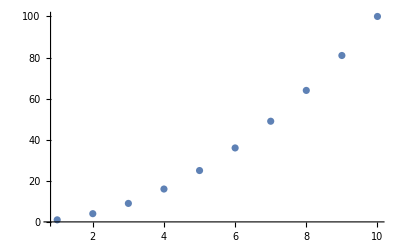

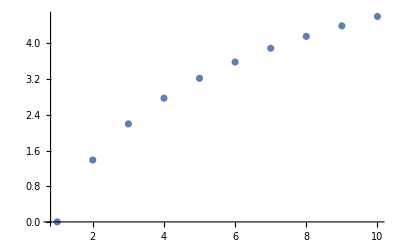

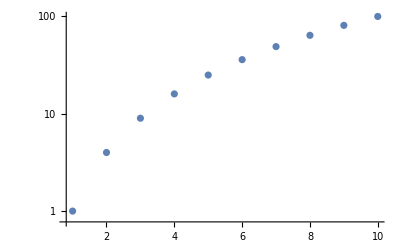

```mathematica
ListPlot[x,ticks2->{ticks2[0,10],ticks2[0,100]}]
ListPlot[x//MapAt[Log,{All,2}],ticks2->{ticks2[#1,#2]&,ticks2["Log",#1,#2]&}]
ListPlot[x,ScalingFunctions->{None,"Log"}]
```

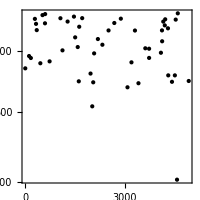

```mathematica
x//MapAt[Log,{All,2}]//
	Point//
	op[Graphics[Frame->True,ImageSize->200,AspectRatio->1,FrameTicks->{{Charting`ScaledTicks["Log"](*Function[Charting`ScaledTicks[{Log, Exp}][#, #2, {6, 6}]]*),None},{Automatic,None}}]]
```

```mathematica
Names["*Transform*"]//TableForm
```

AffineTransform
AudioSpectralTransformation
BottomHatTransform
ConfidenceTransform
ContinuousWaveletTransform
CoordinateTransform
CoordinateTransformData
DirichletTransform
DiscreteChirpZTransform
DiscreteHadamardTransform
DiscreteWaveletPacketTransform
DiscreteWaveletTransform
DistanceTransform
FillingTransform
FindGeometricTransform
FourierCosTransform
FourierSequenceTransform
FourierSinTransform
FourierTransform
GeometricTransformation
GeometricTransformation3DBox
GeometricTransformation3DBoxOptions
GeometricTransformationBox
GeometricTransformationBoxOptions
HankelTransform
HistogramTransform
HistogramTransformInterpolation
HitMissTransform
ImageForwardTransformation
ImagePerspectiveTransformation
ImageTransformation
InverseContinuousWaveletTransform
InverseDistanceTransform
InverseFourierCosTransform
InverseFourierSequenceTransform
InverseFourierSinTransform
InverseFourierTransform
InverseHankelTransform
InverseLaplaceTransform
InverseMellinTransform
InverseRadonTransform
InverseTransformedRegion
InverseWaveletTransform
InverseZTransform
LaplaceTransform
LiftingWaveletTransform
LinearFractionalTransform
LinearizingTransformationData
ListFourierSequenceTransform
ListZTransform
MellinTransform
MorphologicalTransform
NondimensionalizationTransform
RadonTransform
ReflectionTransform
RescalingTransform
RotationTransform
ScalingTransform
ShearingTransform
SkeletonTransform
SpatialTransformationLayer
StateSpaceTransform
StateTransformationLinearize
StationaryWaveletPacketTransform
StationaryWaveletTransform
TopHatTransform
TransferFunctionTransform
TransformationClass
TransformationFunction
TransformationFunctions
TransformationMatrix
TransformedDistribution
TransformedField
TransformedProcess
TransformedRegion
TranslationTransform
ZTransform

```mathematica
ImageForwardTransformation
```